```mathematica
LaunchKernels[]
(*Needs["FourierSeries`"]*)
```

{KernelObject(1,local),KernelObject(2,local)}

```mathematica
(*константы*)
α=1/137;lc=SetPrecision[3.86 10^-11,MachinePrecision];cc=SetPrecision[3 10^(10),MachinePrecision];mee=SetPrecision[0.511 10^6,MachinePrecision];
(*параметры траектории*)
γ=SetPrecision[235,MachinePrecision];(*гамма-фактор заряженных частиц*)
λo=SetPrecision[10^(-3)/lc,MachinePrecision];(*период ондулятора 1 см*)
kdip=SetPrecision[1/1000,MachinePrecision];(*параметр дипольности*)
βp=Sqrt[1-(1+kdip^2)/γ^2];(*составляющая скорости вдоль оси 3*)
ω=(2 π)/λo βp;(*круговая частота колебаний в частиц однуляторе*)
χt=1;(*χt -- киральность спирали траектории; γ=235, K=1.29,lambda_0=3.3cm -- SLAC, Hemsing*)
θi=0;(*угол падения частицы относительно нормали к поверхности*)
No=2;(*число периодов ондулятора*)
Lt=No 2 Pi/ω;(*время пролета ондулятора*)
mMax =10; (*ожидаемое максимальное значение m*)
Print["Магнитное поле в ондуляторе H (Гс): ",(2 Pi Sqrt[2]kdip/λo) 4.41 10^(13)]
```

Магнитное поле в ондуляторе H (Гс): 15125.9

```mathematica
Lz= βp Lt;(*толщина пластины холестерика*)
Nc=25;(*число периодов холестерика*)
qc=Pi Nc/Lz;(*волновой вектор холестерика*)
(*диэлектрическая проницаемость*)
(*ϵc[ω1_?NumberQ]:=SetPrecision[Module[{λ=2 Pi/ω1 lc 10^4},
If[λ≥0.275&&λ≤0.546,(1+0.014755297/(426.29740-λ^(-2)))^2,1]],90](*гелий*)*)
ϵpp[k0_]=SetPrecision[1.1,MachinePrecision];(*перпендикулярная диэлектрическая проницаемость*)
ϵpl[k0_]=SetPrecision[1.5,MachinePrecision];(*параллельная диэлектрическая проницаемость*)
dec[k0_]=(ϵpl[k0]-ϵpp[k0])/ϵpp[k0];(*анизотропия*)
Print["Волновой вектор холестерика в эВ: ",qc mee]
Print["Толщина пластины холестерика в мкм: ",Lz lc 10^4]
Print["Анизотропия de: ",dec[1.5/mee]]
```

Волновой вектор холестерика в эВ: 0.774583

Толщина пластины холестерика в мкм: 20.

Анизотропия de: 0.363636

```mathematica
e3={0,0,1};
e1={1,0,0};
e2={0,1,0};
ep=e1+ⅈ e2;
em=e1-ⅈ e2;
```

```mathematica
xoa=kdip/(Sqrt[2] ω γ);yoa=xoa;(*амплитуды колебаний*)
zo=-Lz;(*начальная координата в компотоновский длинах волн. частица вылетает из пластины в сторону детектора*)
(*xo=0;yo=0;zo=0;начальные координаты в компотоновский длинах волн*)
ωs=χt ω;(*частота со знаком*)
vx0=Sin[θi] Sqrt[1-1/γ^2];vy0=0;vz0=Cos[θi] Sqrt[1-1/γ^2];(*скорость влета*)
rt[t_]={xoa Cos[ωs t],yoa Sin[ωs t],zo+βp t};
v[t_]={-xoa ωs Sin[ωs t],yoa ωs Cos[ωs t],βp};
xo=rt[0][[1]];yo=rt[0][[2]];
```

```mathematica
tfin=Lt;
```

```mathematica
rf=rt[tfin];
vxf=0;vyf=0;vzf=Sqrt[1-1/γ^2];(*вылетает вдоль оси -- нормали к пластине*)
```

```mathematica
xp[t_]=rt[t].ep;
xm[t_]=rt[t].em;
x3[t_]=rt[t].e3;
x0[t_]=t;  (*c=1*)
vp[t_]=v[t].ep;
vm[t_]=v[t].em;
v3[t_]=v[t].e3;
```

```mathematica
k31[k0s_,kp_,de_]=Sqrt[k0s-kp^2];(*правая быстрая ветвь при q=1*)
k32[k0s_,kp_,de_]=2/Pi EllipticE[-kp^2 de/((1+de) (k0s-kp^2))] Sqrt[1+de] Sqrt[k0s-kp^2];(*правая медленная ветвь при q=1*)
```

```mathematica
Clear[CoeffLinComb]
```

```mathematica
CoeffLinComb[s_/;(s^2==1),k00_?NumberQ,k0_?NumberQ,k0s_?NumberQ,kp_?NumberQ,ϕ_?NumberQ,cff_?NumberQ,sff_?NumberQ,ff3_?NumberQ,n3_?NumberQ,k3b_?NumberQ,de_?NumberQ,pf_?NumberQ,ps_?NumberQ]:=Module[{apfs,amfs,apss,amss,amfcs,apfcs,amscs,apscs,rapfs,ramfs,rapss,ramss,ramfcs,rapfcs,ramscs,rapscs,n3i,um,h0i,t0l,tfl,tsl,tpi,tm,gv,ach,al,norm,k320,fac1,fac2,ze,zec,rs},

n3i=1/n3;

(*коэффициенты должны быть вещественными. нужно это учесть*)

(*tf=Exp[-I pf ϕ]; ts=Exp[-I ps ϕ]; r=Exp[-2 I ϕ];*)(*фазовые множители*)
t0l=Exp[-I k00 n3 Lz];tfl=Exp[-I pf qc Lz];tsl=Exp[-I ps qc Lz];

fac1=I Sqrt[k3b/(2 (k0s-kp^2 cff^2))];(*множитель для волны f (1)*)
k320=Sqrt[(1+de) k3b^2+de kp^2 sff^2];(*множитель для волны s (2)*)
fac2=1/Sqrt[2 k320 k0s (k0s-kp^2 cff^2)];
ze=k3b^2 cff+I k0s sff;
zec=k3b^2 cff-I k0s sff;
rs=Exp[I Sqrt[1+de] k3b EllipticE[-ϕ,-kp^2 de/((1+de) k3b^2)]];

apfs=fac1/ff3;(*a_pm при z=0*)
amfs=-fac1 ff3;
apss=fac2 zec rs;
amss=fac2 ze rs;
apfcs=fac1/ff3;(*a_pm сопряженное при z=0*)
amfcs=-fac1 ff3;
apscs=fac2 zec/rs;
amscs=fac2 ze/rs;
(*-I K dz U11 при z=0*)
rapfs=k3b (apfs+kp^2/(2 k3b^2) (apfs+amfs));
ramfs=k3b (amfs+kp^2/(2 k3b^2) (apfs+amfs));
rapss=k320 (apss+kp^2/(2 k3b^2) (apss+amss));
ramss=k320 (amss+kp^2/(2 k3b^2) (apss+amss));
(*U21*)
rapfcs=-k3b (apfcs+kp^2/(2 k3b^2) (apfcs+amfcs));
ramfcs=-k3b (amfcs+kp^2/(2 k3b^2) (apfcs+amfcs));
rapscs=-k320 (apscs+kp^2/(2 k3b^2) (apscs+amscs));
ramscs=-k320 (amscs+kp^2/(2 k3b^2) (apscs+amscs));

um={{apfs,apss,apfcs,apscs},{amfs,amss,amfcs,amscs},{rapfs,rapss,rapfcs,rapscs},{ramfs,ramss,ramfcs,ramscs}};
h0i={{(n3i-1)/(4 √2),(n3i+1)/(4 √2),-(n3i-1)/(4 √2 k0),(n3i+1)/(4 √2 k0)},{(n3i+1)/(4 √2),(n3i-1)/(4 √2),(n3i+1)/(4 √2 k0),-(n3i-1)/(4 √2 k0)},{-(n3i+1)/(4 √2),-(n3i-1)/(4 √2),(n3i+1)/(4 √2 k0),-(n3i-1)/(4 √2 k0)},{-(n3i-1)/(4 √2),-(n3i+1)/(4 √2),-(n3i-1)/(4 √2 k0),(n3i+1)/(4 √2 k0)}};
(*h0={{(n3-1)/(√2),(n3+1)/(√2),(-n3-1)/(√2),(1-n3)/(√2)},{(n3+1)/(√2),(n3-1)/(√2),(1-n3)/(√2),(-n3-1)/(√2)},{(k0 (1-n3))/(√2),(k0 (n3+1))/(√2),(k0 (n3+1))/(√2),(k0 (1-n3))/(√2)},{(k0 (n3+1))/(√2),(k0 (1-n3))/(√2),(k0 (1-n3))/(√2),(k0 (n3+1))/(√2)}};*)

tpi={{1/t0l,0,0,0},{0,1/t0l,0,0},{0,0,t0l,0},{0,0,0,t0l}};
tm={{tfl,0,0,0},{0,tsl,0,0},{0,0,1/tfl,0},{0,0,0,1/tsl}};

gv={(n3-s)/(√2),(n3+s)/(√2),(k0 (1-n3 s))/(√2),(k0 (n3 s+1))/(√2)};

ach=Inverse[um].gv;
(*ach=LinearSolve[um,gv];*)
al=tpi.h0i.um.tm.ach;
norm=Sqrt[2/(1+Conjugate[al].al)];
{norm,ach,al}](*выдает ответ в виде списка. модовые функции безразмерны*)
```

```mathematica
ModeFun1[t_?NumberQ,kp_?NumberQ,ff3_?NumberQ,ctb_?NumberQ,stb_?NumberQ,k0s_?NumberQ,k3b_?NumberQ]:=Module[{fac1,fac13,ff,ff1,apfs,amfs,a3fs,amfcs,apfcs,a3fcs},
ff1=ctb+I stb;
fac1=I Sqrt[k3b/(2 (k0s-kp^2 ctb^2))];
fac13=kp stb/Sqrt[2 k3b (k0s-kp^2 ctb^2)];
ff=Exp[I k3b qc x3[t]];

apfs=fac1 ff ff1;(*a_pm,3*)
amfs=-fac1 ff/ff1;
a3fs=fac13 ff;

apfcs=fac1 ff1/ff;(*a_pm,3 сопряженное*)
amfcs=-fac1/ff1/ff;
a3fcs=-fac13/ff;

{{apfs ff3,amfs/ff3,a3fs},{apfcs ff3,amfcs/ff3,a3fcs}}](*ответ в виде списка без общего фазового множителя*)
```

```mathematica
ModeFun2[tet_?NumberQ,kp_?NumberQ,ff3_?NumberQ,ctb_?NumberQ,stb_?NumberQ,k0s_?NumberQ,k3b_?NumberQ,de_?NumberQ]:=Module[{k320,fac2,fac23,ze,zec,ff,apss,amss,a3ss,amscs,apscs,a3scs},
k320=Sqrt[(1+de) k3b^2+de kp^2 stb^2];
fac2=1/Sqrt[2 k320 k0s (k0s-kp^2 ctb^2)];(*множитель для волны s (2)*)
fac23=-kp ctb Sqrt[k320/(2 k0s (k0s-kp^2 ctb^2))];
ze=k3b^2 ctb-I k0s stb;
zec=k3b^2 ctb+I k0s stb;
ff=Exp[I Sqrt[1+de] k3b EllipticE[tet,-kp^2 de/((1+de) k3b^2)]];

apss=fac2 zec ff;(*a_pm,3*)
amss=fac2 ze ff;
a3ss=fac23 ff;

apscs=fac2 zec/ff;(*a_pm,3 сопряженное*)
amscs=fac2 ze/ff;
a3scs=-fac23/ff;

{{apss ff3,amss/ff3,a3ss},{apscs ff3,amscs/ff3,a3scs}} ](*ответ в виде списка без общего фазового множителя*)
```

```mathematica
Clear[InteGrand]
```

```mathematica
InteGrand[t_?NumberQ,k00_?NumberQ,kpl_,kp_?NumberQ,ϕ_?NumberQ,ff3_?NumberQ,achli_,k3b_?NumberQ,k0s_?NumberQ,de_?NumberQ]:=Module[{θb,stb,ctb,afrl,asrl,vpt,vmt,v3t},
θb=qc x3[t]-ϕ;
stb=Sin[θb];
ctb=Cos[θb];

afrl=ModeFun1[t,kp,ff3,ctb,stb,k0s,k3b];
asrl=ModeFun2[θb,kp,ff3,ctb,stb,k0s,k3b,de];

vpt=vp[t];vmt=vm[t];v3t=v3[t];

(achli[[1]] (1/2 (vpt afrl[[1,2]]+vmt afrl[[1,1]])+v3t afrl[[1,3]])+achli[[3]] (1/2 (vpt afrl[[2,2]]+vmt afrl[[2,1]])+v3t afrl[[2,3]])+achli[[2]] (1/2 (vpt asrl[[1,2]]+vmt asrl[[1,1]])+v3t asrl[[1,3]])+achli[[4]] (1/2 (vpt asrl[[2,2]]+vmt asrl[[2,1]])+v3t asrl[[2,3]])) Exp[-I k00 x0[t]+I (kpl[[1]] rt[t][[1]]+kpl[[2]] rt[t][[2]])]]
```

```mathematica
fps[ss_/;(ss^2==1),cffs_,sffs_,npss_,n3ss_]={cffs n3ss-I ss sffs,sffs n3ss+I ss cffs,-npss}/Sqrt[2];
fms[ss_/;(ss^2==1),cffs_,sffs_,npss_,n3ss_]={-cffs n3ss-I ss sffs,-sffs n3ss+I ss cffs,-npss}/Sqrt[2];
```

```mathematica
AmplitEnd[s1_/;(s1^2==1),k00_?NumberQ,kpl_,alli_,cff_?NumberQ,sff_?NumberQ,nps_?NumberQ,n3s_?NumberQ]:=Module[{contR,contL,contF},
contR=(alli[[1]] fps[1,cff,sff,nps,n3s]+alli[[2]] fps[-1,cff,sff,nps,n3s]).{vx0,vy0,vz0} I Exp[I (k00 n3s zo+kpl[[1]] xo+ kpl[[2]] yo)]/(k00 (1-n3s vz0)-kpl[[1]] vx0- kpl[[2]] vy0);
contL=(alli[[3]] fms[1,cff,sff,nps,n3s]+alli[[4]] fms[-1,cff,sff,nps,n3s]).{vx0,vy0,vz0} I Exp[I (-k00 n3s zo+kpl[[1]] xo+ kpl[[2]] yo)]/(k00 (1+n3s vz0)-kpl[[1]] vx0- kpl[[2]] vy0);(*вклад слева от пластины*)

contF=-I fps[s1,cff,sff,nps,n3s].{vxf,vyf,vzf} Exp[-I (k00 tfin-k00 n3s rf[[3]]-kpl[[1]] rf[[1]]-kpl[[2]] rf[[2]])]/(k00 (1-n3s vzf)-kpl[[1]] vxf- kpl[[2]] vyf);(*вклад справа от пластины*)

contR+contL+contF](*вклад без общего нормировочного множителя*)
```

```mathematica
AmplitPlane[s1_?NumberQ,k00_?NumberQ,npx_?NumberQ,npy_?NumberQ]:=Module[{kpl,ϕ,cff,sff,ff3,k0,k0s,np,n3,kp,k3b,de,pf,ps,coeffList,cnorm,ach,al,amplPlate,amplE},
kpl=k00 {npx,npy};
ϕ=Arg[npx+I npy];cff=Cos[ϕ];sff=Sin[ϕ];ff3=cff+I sff;(*часто используемые постоянные*)
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
np=Sqrt[npx^2+npy^2];
n3=Sqrt[1-np^2];
kp=k0 np;
k3b=Sqrt[k0s-kp^2];
de=dec[k00];
pf=k3b;(*импульсы с q=1*)
ps=2/Pi EllipticE[-kp^2 de/((1+de) k3b^2)] Sqrt[1+de] k3b;

coeffList=CoeffLinComb[s1,k00,k0,k0s,kp,ϕ,cff,sff,ff3,n3,k3b,de,pf,ps];
cnorm=coeffList[[1]];
ach=coeffList[[2]];
al=coeffList[[3]];

amplPlate=NIntegrate[InteGrand[t,k00,kpl,kp,ϕ,ff3,ach,k3b,k0s,de],{t,0,tfin},Method->{"GlobalAdaptive","SingularityHandler"->"IMT","SingularityDepth"->Infinity, "SymbolicProcessing"->0}];(*основной интеграл. возможно, лучше передавать в процедуры t как число*)

amplE=AmplitEnd[s1,k00,kpl,al,cff,sff,np,n3];(*концы*)

cnorm (amplPlate+amplE)](*полная амплитуда без постоянного общего множителя. размерность: 1/энергия*)
```

```mathematica
Clear[dProbabPlane]
```

```mathematica
dProbabPlane[s1_/;(s1^2==1),k001_?NumberQ,npx1_?NumberQ,npy1_?NumberQ]:=Module[{npx,npy,k00,kpl,ϕ,cff,sff,k0,k0s,np,n3,kp,k3b,de,pf,ps,coeffList,cnorm,ach,al,xxl,yyl,amplPlate,amplE},
npx=SetPrecision[npx1,MachinePrecision];
npy=SetPrecision[npy1,MachinePrecision];
k00=SetPrecision[k001,MachinePrecision];

kpl=k00 {npx,npy};
ϕ=Arg[npx+I npy];cff=Cos[ϕ];sff=Sin[ϕ];ff3=cff+I sff;(*часто используемые постоянные*)
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
np=Sqrt[npx^2+npy^2];
n3=Sqrt[1-np^2];
kp=k0 np;
k3b=Sqrt[k0s-kp^2];
de=dec[k00];
pf=k3b;(*импульсы с q=1*)
ps=2/Pi EllipticE[-kp^2 de/((1+de) k3b^2)] Sqrt[1+de] k3b;

coeffList=CoeffLinComb[s1,k00,k0,k0s,kp,ϕ,cff,sff,ff3,n3,k3b,de,pf,ps];
cnorm=coeffList[[1]];
ach=coeffList[[2]];
al=coeffList[[3]];

amplPlate=NIntegrate[InteGrand[t,k00,kpl,kp,ϕ,ff3,ach,k3b,k0s,de],{t,0,tfin},Method->{"GlobalAdaptive","SingularityHandler"->"IMT","SingularityDepth"->Infinity, "SymbolicProcessing"->0}];(*основной интеграл. возможно, лучше передавать в процедуры t как число*)

amplE=AmplitEnd[s1,k00,kpl,al,cff,sff,np,n3];(*концы*)

α/(4 Pi^2)k00 Abs[cnorm(amplPlate+amplE)]^2](*вероятность в единицу телесного угла на единичный интервал энергии*)
```

```mathematica
(*------------конец плосковолнового кода----------------------------------*)
```

```mathematica
(*------------закрученные фотоны------------------------------------------*)
```

```mathematica
Clear[AmplTwistTab]
```

```mathematica
AmplTwistTab[s_/;(s^2==1),k00_?NumberQ,kpp_?NumberQ]:=Module[{Npt,np,amplPlTab,amplTwTab},
np=kpp/k00;
Npt=2^(Floor[Log[2,20 mMax]]);(*число элементов таблицы*)

amplPlTab=ParallelTable[AmplitPlane[s,k00,np Cos[N[2 Pi (n1-1)/Npt]],np Sin[N[2 Pi (n1-1)/Npt]]],{n1,1,Npt}];(*таблица значений плосковолновой амплитуды*)
amplTwTab=-np^(1/2)/2 Chop[Fourier[amplPlTab,FourierParameters->{-1,1}]];(*таблица значений закрученной амплитуды с m=s-1 и m+Npt=m*)

{Npt,amplPlTab,amplTwTab}](*на выходе: {число элементов, табл1, табл2}*)
```

```mathematica
AmplTwist[mm_?IntegerQ,amplli_]:=Module[{Npt=Length[amplli]},
I^(-mm)amplli[[1+Mod[mm,Npt]]]](*амплитуда с правильной фазой*)
```

```mathematica
dProbabTwist[mm_?IntegerQ,amplli_]:=2 α/Pi Abs[AmplTwist[mm,amplli]]^2
```

```mathematica
(*нужно сначала вызвать ll=AmplTwistTab[s,k00,kpp], а потом dProbabTwist[m,ll[[3]]] для нужного значения m*)
```

```mathematica
(*------------конец кода для закрученных фотонов-------------------------------*)
```

```mathematica
spectpp[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=2 γ^2 qc (2nn+1)/(1+γ^2 npp^2-γ^2 (ϵpp[k0]-1));(*при npp=χ энергия резко возрастает до вакуумной*)
spectpl[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=2 γ^2 qc (2nn+1)/(1+γ^2 npp^2-γ^2 (ϵpl[k0]-1));
spect3pp[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=-qc (2nn+1)/(1+ϵpp[k0]^(1/2));
spect3pl[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=-qc (2nn+1)/(1+ϵpl[k0]^(1/2));
```

```mathematica
EqnSpecX[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00-b3 qc (2 nn +1+k31[k0s,kp,de])]
EqnSpecTX[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00-b3 qc (2 nn+1-k31[k0s,kp,de])]
EqnSpecY[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00-b3 qc (2 nn+1+k32[k0s,kp,de])]
EqnSpecTY[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00-b3 qc (2 nn+1-k32[k0s,kp,de])]
```

```mathematica
(*-------примеры-------*)
```

```mathematica
dProbabPlane[1,1.5/mee,1/γ,1/γ]//RepeatedTiming
dProbabPlane[1,1.6/mee,1/γ,1/γ]//RepeatedTiming
dProbabPlane[1,1.4/mee,1/γ,1/γ]//RepeatedTiming
dProbabPlane[1,1.7/mee,1/γ,1/γ]//RepeatedTiming
dProbabPlane[1,1.8/mee,1/γ,1/γ]//RepeatedTiming
dProbabPlane[1,1.9/mee,1/γ,1/γ]//RepeatedTiming
dProbabPlane[1,2.0/mee,1/γ,1/γ]//RepeatedTiming
dProbabPlane[1,2.1/mee,1/γ,1/γ]//RepeatedTiming
dProbabPlane[1,2.2/mee,1/γ,1/γ]//RepeatedTiming
```

{1.028,1.50035×10^6}

{1.03,88465.9}

{1.02,574335.}

{1.029,3.97826×10^6}

{1.8,3.24502×10^6}

{1.027,1.16132×10^6}

{1.1495,6.10291×10^6}

{1.59,4.09592×10^6}

{1.24,1.02957×10^6}

```mathematica
2^(Floor[Log[2,20 mMax]])
```

128

```mathematica
llts1=AmplTwistTab[1,1.5/mee,1.5/mee/γ];
lltsm1=AmplTwistTab[-1,1.5/mee,1.5/mee/γ];
```

```mathematica
tms1=Table[{m,dProbabTwist[m,llts1[[3]]]},{m,-mMax,mMax}];
tmsm1=Table[{m,dProbabTwist[m,lltsm1[[3]]]},{m,-mMax,mMax}];
```

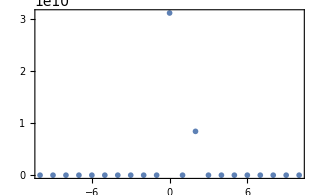
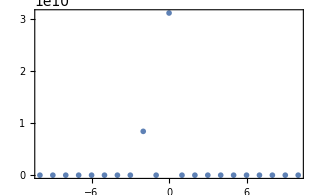

```mathematica
{ListPlot[tms1,Frame->True,Axes->False,PlotRange->Full],ListPlot[tmsm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
llt1s1=AmplTwistTab[1,30/mee,30/mee/5];
llt1sm1=AmplTwistTab[-1,30/mee,30/mee/5];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained 316762.-83059.3 ⅈ and 11268.3 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.75254×10^7}. NIntegrate obtained 339234.-71171.2 ⅈ and 11503.6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.7203×10^7}. NIntegrate obtained 341083.-71642.3 ⅈ and 11526.8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.08462×10^7}. NIntegrate obtained 317174.-81513.8 ⅈ and 11267.8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.16745×10^7}. NIntegrate obtained 342882.-72259.2 ⅈ and 11550.8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.05239×10^7}. NIntegrate obtained 317769.-80021.1 ⅈ and 11264. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.35599×10^7}. NIntegrate obtained 354998.-90687.4 ⅈ and 11736. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.87772×10^7}. NIntegrate obtained 354609.-92186.4 ⅈ and 11733.3 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.5134×10^7}. NIntegrate obtained 333087.-102434. ⅈ and 11503.7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.84549×10^7}. NIntegrate obtained 354043.-93634.2 ⅈ and 11731. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.5134×10^7}. NIntegrate obtained 331231.-101986. ⅈ and 11479.7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.44894×10^7}. NIntegrate obtained 329419.-101389. ⅈ and 11458. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained 316873.-82618.1 ⅈ and 11268.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained 317263.-81067.4 ⅈ and 11267.8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.75254×10^7}. NIntegrate obtained 338986.-70776.4 ⅈ and 11503.6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.05239×10^7}. NIntegrate obtained 317836.-79570.6 ⅈ and 11264.1 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.7203×10^7}. NIntegrate obtained 340816.-71259.1 ⅈ and 11526.8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.16745×10^7}. NIntegrate obtained 342594.-71888.5 ⅈ and 11550.8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.35599×10^7}. NIntegrate obtained 354527.-90567.5 ⅈ and 11736. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.87772×10^7}. NIntegrate obtained 354133.-92088.1 ⅈ and 11733.3 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.84549×10^7}. NIntegrate obtained 353564.-93557.9 ⅈ and 11731. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.5134×10^7}. NIntegrate obtained 332681.-102662. ⅈ and 11503.7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.5134×10^7}. NIntegrate obtained 330839.-102233. ⅈ and 11479.7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.44894×10^7}. NIntegrate obtained 329041.-101655. ⅈ and 11458. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.39872×10^6}. NIntegrate obtained -300938.+74769.3 ⅈ and 11264.7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.75555×10^6}. NIntegrate obtained -53682.8-335184. ⅈ and 11501.4 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained -307479.+42074.2 ⅈ and 11260.4 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.02951×10^7}. NIntegrate obtained -21187.2-341422. ⅈ and 11541.8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.96505×10^7}. NIntegrate obtained 11738.7-344446. ⅈ and 11546.6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.3616×10^7}. NIntegrate obtained -310757.+8893.62 ⅈ and 11269.5 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.6652×10^7}. NIntegrate obtained 353164.-89722.8 ⅈ and 11734.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.23642×10^7}. NIntegrate obtained 110585.+318906. ⅈ and 11502.6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.60074×10^7}. NIntegrate obtained 359607.-57513.9 ⅈ and 11733.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.20419×10^7}. NIntegrate obtained 78151.1+325623. ⅈ and 11480.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.56851×10^7}. NIntegrate obtained 362885.-24828.2 ⅈ and 11737.3 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.72592×10^7}. NIntegrate obtained 45190.1+329129. ⅈ and 11456.9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.39872×10^6}. NIntegrate obtained -301052.+74323.5 ⅈ and 11264.7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.75555×10^6}. NIntegrate obtained -53291.6-334932. ⅈ and 11501.4 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained -307526.+41616.4 ⅈ and 11260.4 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.02951×10^7}. NIntegrate obtained -20836.6-341114. ⅈ and 11541.8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.3616×10^7}. NIntegrate obtained -310735.+8434.1 ⅈ and 11269.5 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.96505×10^7}. NIntegrate obtained 12040.9-344088. ⅈ and 11546.6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.6652×10^7}. NIntegrate obtained 352693.-89602.8 ⅈ and 11734.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.23642×10^7}. NIntegrate obtained 110808.+318496. ⅈ and 11502.6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.60074×10^7}. NIntegrate obtained 359124.-57461.9 ⅈ and 11733.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.20419×10^7}. NIntegrate obtained 78431.6+325252. ⅈ and 11480.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.56851×10^7}. NIntegrate obtained 362400.-24845.2 ⅈ and 11737.3 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.72592×10^7}. NIntegrate obtained 45521.8+328804. ⅈ and 11456.9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
tm1s1=Table[{m,dProbabTwist[m,llt1s1[[3]]]},{m,-mMax,mMax}];
tm1sm1=Table[{m,dProbabTwist[m,llt1sm1[[3]]]},{m,-mMax,mMax}];
```

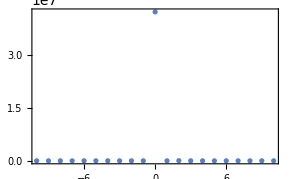
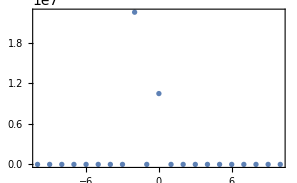

```mathematica
{ListPlot[tm1s1,Frame->True,Axes->False,PlotRange->Full],ListPlot[tm1sm1,Frame->True,Axes->False,PlotRange->Full]}
```

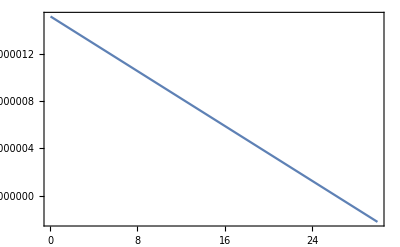

```mathematica
Plot[EqnSpecX[xx/mee,1/5,-1],{xx,1/20,30},Frame->True,PlotRange->Full]
```

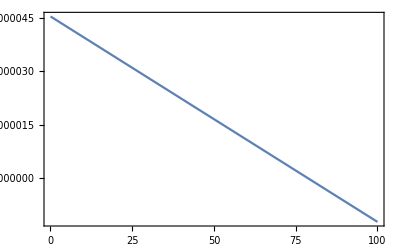

```mathematica
Plot[EqnSpecX[xx/mee,1/5,-2],{xx,1/20,100},Frame->True,PlotRange->Full]
```

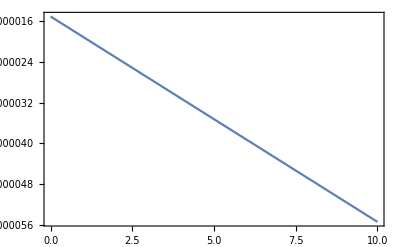

```mathematica
Plot[EqnSpecY[xx/mee,1/5,0],{xx,0/20,10},Frame->True,PlotRange->Full,PlotPoints->100]
```

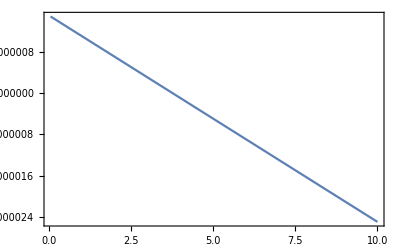

```mathematica
Plot[EqnSpecY[xx/mee,1/5,-1],{xx,1/20,10},Frame->True,PlotRange->Full]
```

```mathematica
4 0.36/0.77
```

1.87013

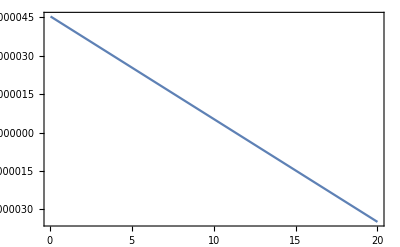

```mathematica
Plot[EqnSpecY[xx/mee,1/5,-2],{xx,1/20,20},Frame->True,PlotRange->Full]
```

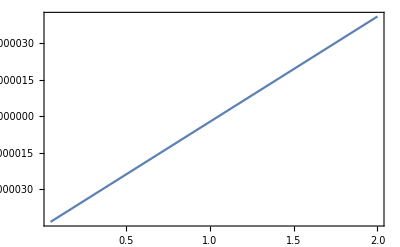

```mathematica
Plot[EqnSpecTY[xx/mee,1/5,1],{xx,1/20,2},Frame->True,PlotRange->Full]
```

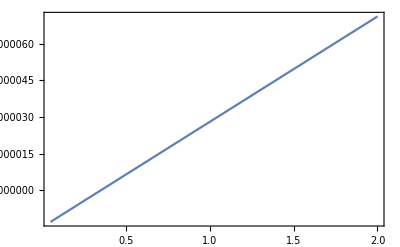

```mathematica
Plot[EqnSpecTY[xx/mee,1/5,0],{xx,1/20,2},Frame->True,PlotRange->Full]
```

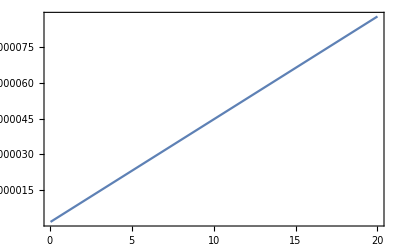

```mathematica
Plot[EqnSpecTY[xx/mee,1/5,-1],{xx,1/20,20},Frame->True,PlotRange->Full]
```

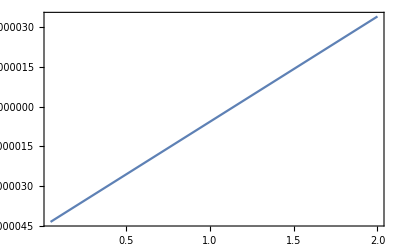

```mathematica
Plot[EqnSpecTX[xx/mee,1/5,1],{xx,1/20,2},Frame->True,PlotRange->Full]
```

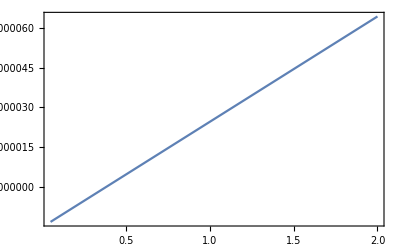

```mathematica
Plot[EqnSpecTX[xx/mee,1/5,0],{xx,1/20,2},Frame->True,PlotRange->Full]
```

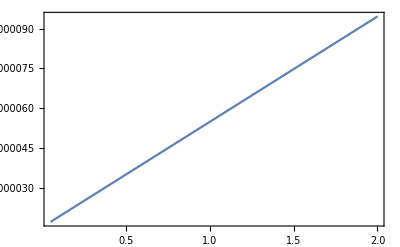

```mathematica
Plot[EqnSpecTX[xx/mee,1/5,-1],{xx,1/20,2},Frame->True,PlotRange->Full]
```

```mathematica
spectpl[1.5/mee,1/5,0] mee
spectpp[1.5/mee,1/5,0] mee
spectpl[1.5/mee,1/5,-1] mee
spectpp[1.5/mee,1/5,-1] mee
spect3pl[1.5/mee,1/5,-1] mee
spect3pp[1.5/mee,1/5,-1] mee
```

-3.3678857525609899308172939535832547389787129429361042273473069072958265269055638669317677

-25.82723557114880604857100363496592890087638165999410510450125200023270914044947575026135

3.3678857525609899308172939535832547389787129429361042273473069072958265269055638669317677

25.82723557114880604857100363496592890087638165999410510450125200023270914044947575026135

0.34816721712587189946825812554907012118106384195547023587877777244136158198254150450133933

0.37806515301769965441355125647507918119448355140262175100352464301008040472872494893776441

```mathematica
spectpl[1.5/mee,1/5,-2] mee
spectpp[1.5/mee,1/5,-1] mee
```

10.103657257682969792451881860749764216936138828808312682041920721887479580716691600795303

25.82723557114880604857100363496592890087638165999410510450125200023270914044947575026135

```mathematica
ϵpp[1.5/mee]-1
ϵpl[1.5/mee]-1
```

0.100000000000000088817841970012523233890533447265625

0.5

```mathematica
tk0s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/5,0]},{x,10,15,0.05}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained 112809.-125758. ⅈ and 0.905904 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.0745×10^7}. NIntegrate obtained -126459.-55965. ⅈ and 0.49679 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained -38857.8-165423. ⅈ and 0.520334 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained 189295.+38186. ⅈ and 0.947146 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained 110169.-138029. ⅈ and 0.544908 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained 76599.4+180166. ⅈ and 0.989359 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained 42591.5+105303. ⅈ and 1.59235 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained 106080.+29278.9 ⅈ and 2.71038 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained -58252.2+114801. ⅈ and 1.66176 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.90433×10^7}. NIntegrate obtained 3676.4+89723.2 ⅈ and 2.82212 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained -119582.+46526.1 ⅈ and 1.73276 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.90433×10^7}. NIntegrate obtained -99985.3+16261.5 ⅈ and 2.93761 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained -146370.+135798. ⅈ and 4.48414 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained -155278.-68614.3 ⅈ and 4.65696 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.53177×10^7}. NIntegrate obtained -46474.7-116977. ⅈ and 7.23003 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained 23712.-158550. ⅈ and 4.83749 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained 53372.6-69059.8 ⅈ and 7.49073 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.18131×10^7}. NIntegrate obtained 52378.4+24138.1 ⅈ and 7.76315 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained -56511.3-21641.8 ⅈ and 11.007 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained -22311.6-96029.2 ⅈ and 11.3852 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.90433×10^7}. NIntegrate obtained -144200.-117788. ⅈ and 16.4192 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained 79531.-101415. ⅈ and 11.7723 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained 70795.5-179574. ⅈ and 16.9707 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained 220054.-2815.56 ⅈ and 17.5338 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

(10. | 72.2302
10.05 | 598.124
10.1 | 1115.25
10.15 | 1111.91
10.2 | 614.295
10.25 | 124.851
10.3 | 100.333
10.35 | 499.561
10.4 | 856.234
10.45 | 784.49
10.5 | 373.952
10.55 | 81.7961
10.6 | 235.126
10.65 | 678.474
10.7 | 936.949
10.75 | 724.336
10.8 | 249.141
10.85 | 20.4861
10.9 | 328.352
10.95 | 930.245
11. | 1262.64
11.05 | 994.69
11.1 | 367.587
11.15 | 2.1579
11.2 | 304.133
11.25 | 1050.85
11.3 | 1572.86
11.35 | 1390.03
11.4 | 670.004
11.45 | 91.0357
11.5 | 194.741
11.55 | 876.39
11.6 | 1492.1
11.65 | 1474.54
11.7 | 843.627
11.75 | 176.082
11.8 | 49.9882
11.85 | 524.796
11.9 | 1116.38
11.95 | 1267.31
12. | 847.602
12.05 | 253.778
12.1 | 4.05388
12.15 | 255.051
12.2 | 688.268
12.25 | 855.133
12.3 | 611.897
12.35 | 229.449
12.4 | 77.1383
12.45 | 247.06
12.5 | 494.3
12.55 | 527.344
12.6 | 319.185
12.65 | 122.869
12.7 | 179.99
12.75 | 450.973
12.8 | 648.418
12.85 | 541.297
12.9 | 216.829
12.95 | 24.2165
13. | 222.561
13.05 | 691.572
13.1 | 1012.43
13.15 | 867.841
13.2 | 376.384
13.25 | 16.5017
13.3 | 171.315
13.35 | 748.69
13.4 | 1247.37
13.45 | 1217.69
13.5 | 683.779
13.55 | 133.066
13.6 | 64.0864
13.65 | 539.366
13.7 | 1132.4
13.75 | 1314.
13.8 | 924.783
13.85 | 314.072
13.9 | 5.97624
13.95 | 232.891
14. | 740.496
14.05 | 1043.32
14.1 | 874.107
14.15 | 407.45
14.2 | 53.3038
14.25 | 70.6255
14.3 | 356.337
14.35 | 593.16
14.4 | 568.948
14.45 | 349.676
14.5 | 159.994
14.55 | 143.584
14.6 | 241.662
14.65 | 296.658
14.7 | 245.067
14.75 | 182.713
14.8 | 235.92
14.85 | 392.617
14.9 | 489.643
14.95 | 387.007
15. | 153.154)

```mathematica
tk0sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/5,0]},{x,10,15,0.05}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.90433×10^7}. NIntegrate obtained 178564.-81373.2 ⅈ and 0.495502 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.70194×10^7}. NIntegrate obtained -109067.+213582. ⅈ and 0.90385 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained 121883.+118275. ⅈ and 0.520334 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained -203745.-19890.7 ⅈ and 0.945307 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained -90681.5+141595. ⅈ and 0.546236 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained -32438.3-191086. ⅈ and 0.989148 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained -4694.56-32990.9 ⅈ and 1.5915 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.70194×10^7}. NIntegrate obtained 25529.6+34869.3 ⅈ and 1.6589 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained -138194.-55118.6 ⅈ and 2.71319 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.70194×10^7}. NIntegrate obtained -40864.8+77649.9 ⅈ and 1.72995 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained -24712.9-193947. ⅈ and 2.82129 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.0745×10^7}. NIntegrate obtained 167356.-141142. ⅈ and 2.93354 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained 234415.-111486. ⅈ and 4.4904 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.0745×10^7}. NIntegrate obtained 227799.+172876. ⅈ and 4.66161 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.65958×10^7}. NIntegrate obtained -34542.6+286764. ⅈ and 4.83686 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained -68199.9+134255. ⅈ and 7.23417 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained -155862.+6404.76 ⅈ and 7.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained -81940.8-112045. ⅈ and 7.7707 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained 89348.4-81597.8 ⅈ and 10.9941 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained 118448.+34686.5 ⅈ and 11.3786 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained 216131.+188553. ⅈ and 16.4217 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained 9421.91+113006. ⅈ and 11.7773 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained -59763.5+288176. ⅈ and 16.9577 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.11685×10^7}. NIntegrate obtained -269249.+76241.6 ⅈ and 17.5142 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

(10. | 700.083
10.05 | 1939.74
10.1 | 2697.63
10.15 | 2261.78
10.2 | 1054.07
10.25 | 262.912
10.3 | 704.032
10.35 | 2006.05
10.4 | 2941.48
10.45 | 2623.33
10.5 | 1355.5
10.55 | 353.314
10.6 | 561.527
10.65 | 1744.58
10.7 | 2736.94
10.75 | 2589.27
10.8 | 1442.27
10.85 | 366.229
10.9 | 315.17
10.95 | 1235.35
11. | 2160.26
11.05 | 2166.95
11.1 | 1236.34
11.15 | 250.672
11.2 | 105.039
11.25 | 836.902
11.3 | 1624.82
11.35 | 1644.54
11.4 | 886.498
11.45 | 144.247
11.5 | 169.654
11.55 | 903.095
11.6 | 1555.79
11.65 | 1443.49
11.7 | 683.522
11.75 | 83.8781
11.8 | 310.851
11.85 | 1204.83
11.9 | 1918.54
11.95 | 1757.93
12. | 882.455
12.05 | 199.781
12.1 | 474.415
12.15 | 1546.9
12.2 | 2444.76
12.25 | 2323.63
12.3 | 1305.72
12.35 | 409.961
12.4 | 553.943
12.45 | 1654.59
12.5 | 2698.92
12.55 | 2718.84
12.6 | 1703.98
12.65 | 620.548
12.7 | 470.075
12.75 | 1358.34
12.8 | 2415.89
12.85 | 2628.2
12.9 | 1777.78
12.95 | 648.662
13. | 248.013
13.05 | 856.655
13.1 | 1785.02
13.15 | 2070.79
13.2 | 1415.13
13.25 | 453.835
13.3 | 75.4242
13.35 | 545.128
13.4 | 1281.22
13.45 | 1483.99
13.5 | 942.79
13.55 | 222.341
13.6 | 48.9629
13.65 | 574.866
13.7 | 1235.19
13.75 | 1334.
13.8 | 764.325
13.85 | 139.216
13.9 | 167.97
13.95 | 917.571
14. | 1703.77
14.05 | 1759.27
14.1 | 1033.91
14.15 | 294.346
14.2 | 369.962
14.25 | 1312.69
14.3 | 2308.12
14.35 | 2446.5
14.4 | 1622.02
14.45 | 658.284
14.5 | 521.035
14.55 | 1406.13
14.6 | 2539.97
14.65 | 2886.85
14.7 | 2128.9
14.75 | 972.62
14.8 | 480.818
14.85 | 1085.11
14.9 | 2174.82
14.95 | 2678.93
15. | 2099.43)

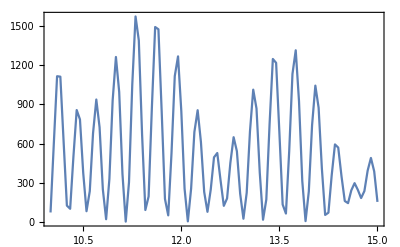
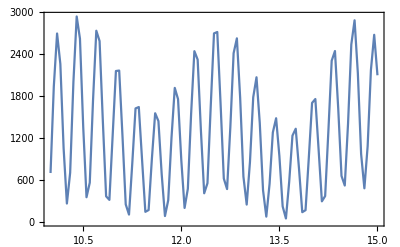

```mathematica
{ListLinePlot[tk0s1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[tk0sm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
tk01s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/5,0]},{x,15,20,0.05}](*-2 гармоники не видно, т.к. соотв. коэффициент Фурье очень мал*)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained -196434.-115560. ⅈ and 23.344 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained 35045.2-51371.7 ⅈ and 34.7895 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained 5803.57-199639. ⅈ and 24.0772 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained 42683.9-25926.1 ⅈ and 35.8289 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained 157861.-60964.6 ⅈ and 24.8402 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained 46314.4-11445.2 ⅈ and 36.8975 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained 100413.-151902. ⅈ and 50.9299 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained 213732.+33928.6 ⅈ and 52.4016 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained 111494.+224137. ⅈ and 73.3192 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained 84301.1+229894. ⅈ and 53.8893 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained -170656.+202541. ⅈ and 75.3978 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.0745×10^7}. NIntegrate obtained -269070.-60176.6 ⅈ and 77.4778 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained -80098.7-6435.37 ⅈ and 103.21 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained -19964.2-74963.4 ⅈ and 105.957 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained 49132.5-54836.6 ⅈ and 108.954 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained -155011.+136556. ⅈ and 145.425 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained -194180.-76112.1 ⅈ and 149.112 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.70194×10^7}. NIntegrate obtained -3299.92-210880. ⅈ and 152.865 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained -335948.-130431. ⅈ and 195.771 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained -42005.7-356639. ⅈ and 200.606 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained 286800.-187224. ⅈ and 205.548 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained -26216.3-242471. ⅈ and 260.875 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained 195776.-132864. ⅈ and 267.076 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained 192155.+93159. ⅈ and 273.395 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

(15. | 153.154
15.05 | 33.2544
15.1 | 209.428
15.15 | 588.58
15.2 | 854.056
15.25 | 752.227
15.3 | 357.798
15.35 | 30.6839
15.4 | 98.6994
15.45 | 549.54
15.5 | 1021.45
15.55 | 1109.05
15.6 | 732.979
15.65 | 217.785
15.7 | 14.8438
15.75 | 305.595
15.8 | 836.328
15.85 | 1140.44
15.9 | 957.497
15.95 | 451.688
16. | 51.6928
16.05 | 68.776
16.1 | 436.975
16.15 | 802.97
16.2 | 854.49
16.25 | 570.497
16.3 | 198.148
16.35 | 16.5216
16.4 | 107.911
16.45 | 334.127
16.5 | 491.789
16.55 | 481.585
16.6 | 350.75
16.65 | 210.331
16.7 | 128.307
16.75 | 110.483
16.8 | 146.966
16.85 | 240.189
16.9 | 373.533
16.95 | 474.982
17. | 448.124
17.05 | 273.691
17.1 | 72.31
17.15 | 30.7648
17.2 | 239.032
17.25 | 579.614
17.3 | 793.752
17.35 | 694.173
17.4 | 347.859
17.45 | 42.7479
17.5 | 61.384
17.55 | 427.519
17.6 | 863.406
17.65 | 1011.89
17.7 | 747.469
17.75 | 286.464
17.8 | 15.3549
17.85 | 158.668
17.9 | 592.217
17.95 | 954.501
18. | 955.589
18.05 | 601.421
18.1 | 177.979
18.15 | 3.9694
18.2 | 184.158
18.25 | 549.321
18.3 | 808.659
18.35 | 770.582
18.4 | 476.341
18.45 | 144.925
18.5 | 1.74368
18.55 | 126.091
18.6 | 411.409
18.65 | 651.56
18.7 | 684.055
18.75 | 490.657
18.8 | 201.53
18.85 | 14.9096
18.9 | 64.5498
18.95 | 328.072
19. | 632.042
19.05 | 763.924
19.1 | 619.845
19.15 | 297.891
19.2 | 36.8879
19.25 | 48.1837
19.3 | 347.974
19.35 | 728.179
19.4 | 901.898
19.45 | 732.726
19.5 | 346.613
19.55 | 43.8277
19.6 | 65.2287
19.65 | 398.526
19.7 | 787.802
19.75 | 938.446
19.8 | 740.351
19.85 | 345.486
19.9 | 48.1549
19.95 | 60.3829
20. | 367.361)

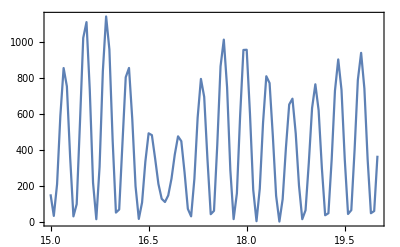

```mathematica
ListLinePlot[tk01s1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk01sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/5,0]},{x,15,20,0.05}](*-2 гармоники не видно, т.к. соотв. коэффициент Фурье очень мал*)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained -24319.7-36348.5 ⅈ and 34.7628 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained 166509.+166560. ⅈ and 23.3497 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained 29618.1-42080.3 ⅈ and 35.8345 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.70194×10^7}. NIntegrate obtained -94205.4+230658. ⅈ and 24.1013 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained 37436.3+6566.55 ⅈ and 36.9336 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.24467×10^7}. NIntegrate obtained -254632.+24382.4 ⅈ and 24.865 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.11685×10^7}. NIntegrate obtained -73426.3+243392. ⅈ and 50.8668 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained -163366.-285904. ⅈ and 73.2643 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained -246371.+42239.1 ⅈ and 52.3508 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained 170702.-252011. ⅈ and 75.2596 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained -127360.-207779. ⅈ and 53.8926 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained 272782.+56304.5 ⅈ and 77.3526 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained 124791.+28294.1 ⅈ and 104.707 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained 22643.9+82380.7 ⅈ and 107.498 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained 144070.-136919. ⅈ and 145.3 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained -40493.+20172.8 ⅈ and 110.155 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained 218016.+97051.8 ⅈ and 149.043 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained 13578.6+275669. ⅈ and 152.887 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained 342094.+120059. ⅈ and 195.777 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained 14978.4+367731. ⅈ and 200.59 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.70194×10^7}. NIntegrate obtained 35053.5+255875. ⅈ and 260.887 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.11685×10^7}. NIntegrate obtained -346786.+167920. ⅈ and 205.492 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained -194570.+109002. ⅈ and 267.085 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained -152611.-134546. ⅈ and 273.406 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

(15. | 2099.43
15.05 | 969.106
15.1 | 303.29
15.15 | 627.715
15.2 | 1501.17
15.25 | 1991.09
15.3 | 1598.06
15.35 | 696.534
15.4 | 110.668
15.45 | 302.679
15.5 | 952.052
15.55 | 1320.85
15.6 | 1011.47
15.65 | 346.082
15.7 | 12.8155
15.75 | 348.101
15.8 | 982.866
15.85 | 1228.69
15.9 | 818.842
15.95 | 207.38
16. | 111.137
16.05 | 749.156
16.1 | 1577.44
16.15 | 1813.24
16.2 | 1248.45
16.25 | 486.039
16.3 | 376.682
16.35 | 1178.55
16.4 | 2265.06
16.45 | 2683.63
16.5 | 2078.67
16.55 | 1047.3
16.6 | 618.078
16.65 | 1280.13
16.7 | 2484.84
16.75 | 3134.12
16.8 | 2634.12
16.85 | 1450.31
16.9 | 682.61
16.95 | 1018.48
17. | 2085.4
17.05 | 2829.31
17.1 | 2534.81
17.15 | 1455.98
17.2 | 545.345
17.25 | 535.175
17.3 | 1275.65
17.35 | 1934.73
17.4 | 1822.6
17.45 | 1015.7
17.5 | 245.838
17.55 | 154.063
17.6 | 675.311
17.65 | 1152.32
17.7 | 1040.29
17.75 | 454.533
17.8 | 25.783
17.85 | 207.047
17.9 | 790.301
17.95 | 1135.99
18. | 871.243
18.05 | 299.692
18.1 | 110.554
18.15 | 652.998
18.2 | 1536.87
18.25 | 1981.02
18.3 | 1593.92
18.35 | 799.929
18.4 | 494.562
18.45 | 1168.41
18.5 | 2373.03
18.55 | 3092.41
18.6 | 2710.16
18.65 | 1628.67
18.7 | 951.
18.75 | 1421.51
18.8 | 2696.57
18.85 | 3655.6
18.9 | 3450.3
18.95 | 2283.39
19. | 1234.06
19.05 | 1227.49
19.1 | 2197.79
19.15 | 3182.39
19.2 | 3221.93
19.25 | 2224.75
19.3 | 1041.23
19.35 | 626.868
19.4 | 1168.89
19.45 | 1959.42
19.5 | 2114.73
19.55 | 1421.15
19.6 | 500.238
19.65 | 127.197
19.7 | 471.818
19.75 | 991.355
19.8 | 1046.21
19.85 | 562.786
19.9 | 73.0772
19.95 | 110.065
20. | 635.393)

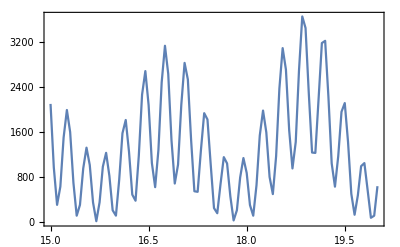

```mathematica
ListLinePlot[tk01sm1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk02s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/5,0]},{x,20,25,0.05}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.0745×10^7}. NIntegrate obtained -9202.37+69763.4 ⅈ and 336.43 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.564×10^7}. NIntegrate obtained -356422.-204683. ⅈ and 449.731 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.90433×10^7}. NIntegrate obtained -77043.4+47690.1 ⅈ and 344.155 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained 20297.5-421757. ⅈ and 459.652 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained -88619.7-53159.2 ⅈ and 352.043 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.65958×10^7}. NIntegrate obtained 388678.-162762. ⅈ and 469.807 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained 412533.-187763. ⅈ and 594.832 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.24467×10^7}. NIntegrate obtained 338382.+269931. ⅈ and 607.508 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained -3430.5+74196.5 ⅈ and 779.107 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained -89147.5+389836. ⅈ and 620.391 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.94668×10^7}. NIntegrate obtained -18853.3+33849.6 ⅈ and 795.052 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained -7656.37+47047.2 ⅈ and 811.037 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained 295570.+394979. ⅈ and 1010.22 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained -266519.+465647. ⅈ and 1030.25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained -584750.-52114.2 ⅈ and 1050.63 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.90433×10^7}. NIntegrate obtained -756073.+4509.67 ⅈ and 1298.4 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained -308751.-688644. ⅈ and 1323.36 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained 500238.-569601. ⅈ and 1348.5 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.65958×10^7}. NIntegrate obtained -196671.-321500. ⅈ and 1624.62 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained 173996.-249592. ⅈ and 1654.7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained 234880.+51694.7 ⅈ and 1685.14 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained -392071.+501987. ⅈ and 2018.32 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained -738206.-168292. ⅈ and 2054.55 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained -196291.-851073. ⅈ and 2091.25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

(20. | 367.361
20.05 | 747.524
20.1 | 932.127
20.15 | 790.206
20.2 | 422.961
20.25 | 90.1925
20.3 | 40.5136
20.35 | 332.931
20.4 | 781.579
20.45 | 1071.27
20.5 | 987.993
20.55 | 584.063
20.6 | 169.515
20.65 | 89.5586
20.7 | 451.833
20.75 | 1020.95
20.8 | 1384.17
20.85 | 1262.9
20.9 | 751.4
20.95 | 261.599
21. | 202.668
21.05 | 653.797
21.1 | 1282.87
21.15 | 1595.5
21.2 | 1339.34
21.25 | 718.658
21.3 | 225.526
21.35 | 243.934
21.4 | 731.175
21.45 | 1264.52
21.5 | 1403.28
21.55 | 1044.76
21.6 | 470.676
21.65 | 99.7064
21.7 | 147.843
21.75 | 500.482
21.8 | 850.26
21.85 | 947.548
21.9 | 747.846
21.95 | 398.228
22. | 102.713
22.05 | 11.1942
22.1 | 173.664
22.15 | 529.651
22.2 | 910.071
22.25 | 1092.97
22.3 | 935.946
22.35 | 527.764
22.4 | 214.002
22.45 | 369.88
22.5 | 1071.46
22.55 | 1949.08
22.6 | 2417.81
22.65 | 2151.26
22.7 | 1434.64
22.75 | 986.953
22.8 | 1391.91
22.85 | 2564.93
22.9 | 3736.17
22.95 | 4042.58
23. | 3303.67
23.05 | 2212.12
23.1 | 1802.17
23.15 | 2557.58
23.2 | 3937.4
23.25 | 4812.33
23.3 | 4465.44
23.35 | 3188.64
23.4 | 2038.63
23.45 | 1911.9
23.5 | 2768.69
23.55 | 3724.51
23.6 | 3861.27
23.65 | 2970.24
23.7 | 1675.76
23.75 | 836.88
23.8 | 811.375
23.85 | 1261.67
23.9 | 1566.1
23.95 | 1387.96
24. | 884.123
24.05 | 414.669
24.1 | 150.971
24.15 | 37.7345
24.2 | 62.0312
24.25 | 423.764
24.3 | 1310.
24.35 | 2517.46
24.4 | 3431.22
24.45 | 3591.8
24.5 | 3335.39
24.55 | 3745.43
24.6 | 5811.89
24.65 | 9390.7
24.7 | 12990.5
24.75 | 14955.9
24.8 | 15051.8
24.85 | 14930.4
24.9 | 17038.8
24.95 | 22358.
25. | 29128.8)

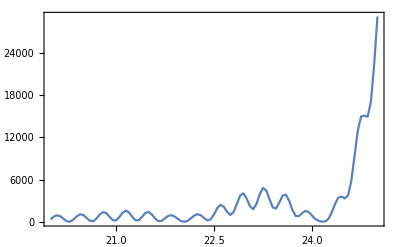

```mathematica
ListLinePlot[tk02s1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk02sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/5,0]},{x,20,25,0.05}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained 363282.+184815. ⅈ and 449.739 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained -25954.5-30105.1 ⅈ and 336.44 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained -34064.2+430867. ⅈ and 459.682 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained 58619.8-44834.6 ⅈ and 344.164 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained 106208.+63590.2 ⅈ and 352.053 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained -437900.+156609. ⅈ and 469.828 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained -414602.+174160. ⅈ and 594.814 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained 25167.2-36982.3 ⅈ and 778.674 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained -313373.-308621. ⅈ and 607.486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained 8448.68+29063.6 ⅈ and 794.586 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained 152399.-409094. ⅈ and 620.449 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained -43325.9-2965.92 ⅈ and 811.12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained -344559.-430935. ⅈ and 1010.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained 818527.+9186.63 ⅈ and 1298.44 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained 250527.-529726. ⅈ and 1030.24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained 341268.+730904. ⅈ and 1323.32 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained 607993.+3650.34 ⅈ and 1050.57 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.11685×10^7}. NIntegrate obtained -501575.+598285. ⅈ and 1348.54 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained 157684.+370570. ⅈ and 1624.59 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.90433×10^7}. NIntegrate obtained 366549.-557583. ⅈ and 2018.51 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.24467×10^7}. NIntegrate obtained -226031.+260346. ⅈ and 1654.57 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained 752017.+116734. ⅈ and 2054.52 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained -260950.-65871.5 ⅈ and 1685.1 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained 221882.+832890. ⅈ and 2091.16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

(20. | 635.393
20.05 | 1082.66
20.1 | 968.656
20.15 | 439.614
20.2 | 168.612
20.25 | 659.44
20.3 | 1667.99
20.35 | 2371.21
20.4 | 2165.91
20.45 | 1340.7
20.5 | 879.687
20.55 | 1506.08
20.6 | 2924.24
20.65 | 4035.21
20.7 | 3943.39
20.75 | 2849.21
20.8 | 1907.06
20.85 | 2143.86
20.9 | 3505.98
20.95 | 4881.85
21. | 5080.39
21.05 | 3942.43
21.1 | 2496.74
21.15 | 2004.63
21.2 | 2829.92
21.25 | 4105.66
21.3 | 4537.34
21.35 | 3629.71
21.4 | 2113.07
21.45 | 1198.41
21.5 | 1455.24
21.55 | 2327.93
21.6 | 2745.18
21.65 | 2176.88
21.7 | 1067.29
21.75 | 306.457
21.8 | 352.343
21.85 | 844.029
21.9 | 1059.48
21.95 | 694.499
22. | 148.107
22.05 | 52.2281
22.1 | 556.595
22.15 | 1140.51
22.2 | 1179.58
22.25 | 690.981
22.3 | 400.98
22.35 | 1008.7
22.4 | 2379.54
22.45 | 3558.12
22.5 | 3666.83
22.55 | 2867.23
22.6 | 2295.88
22.65 | 3023.73
22.7 | 4987.65
22.75 | 6918.94
22.8 | 7433.49
22.85 | 6377.41
22.9 | 5008.99
22.95 | 4927.15
23. | 6605.14
23.05 | 8841.07
23.1 | 9792.86
23.15 | 8719.19
23.2 | 6632.72
23.25 | 5421.77
23.3 | 6123.31
23.35 | 7938.17
23.4 | 9016.03
23.45 | 8206.97
23.5 | 6005.75
23.55 | 4053.61
23.6 | 3604.59
23.65 | 4420.54
23.7 | 5144.9
23.75 | 4648.88
23.8 | 3007.77
23.85 | 1340.71
23.9 | 654.407
23.95 | 907.671
24. | 1219.45
24.05 | 910.093
24.1 | 235.584
24.15 | 47.8898
24.2 | 756.633
24.25 | 1800.96
24.3 | 2274.56
24.35 | 2067.87
24.4 | 2201.97
24.45 | 3900.82
24.5 | 7230.42
24.55 | 10732.
24.6 | 12696.
24.65 | 12926.8
24.7 | 13176.3
24.75 | 15829.3
24.8 | 21579.5
24.85 | 28344.7
24.9 | 32991.5
24.95 | 34212.2
25. | 33901.6)

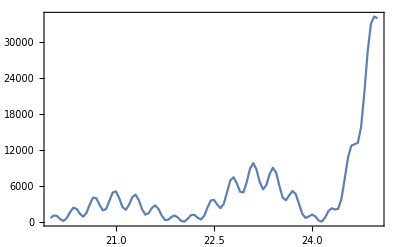

```mathematica
ListLinePlot[tk02sm1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk03s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/5,0]},{x,25,30,0.05}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained -1.0117×10^6-2.87841×10^6 ⅈ and 3054.75 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.94668×10^7}. NIntegrate obtained -1.00647×10^6+1.55899×10^6 ⅈ and 2448.64 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.70194×10^7}. NIntegrate obtained 2.23888×10^6-2.15597×10^6 ⅈ and 3106.1 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.24467×10^7}. NIntegrate obtained -1.93854×10^6-286851. ⅈ and 2490.46 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained 2.95154×10^6+1.16281×10^6 ⅈ and 3157.26 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained -574363.-1.99342×10^6 ⅈ and 2533.65 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained 3.22491×10^6+1.08179×10^6 ⅈ and 3785.79 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained 354763.+3.36019×10^6 ⅈ and 3856.22 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained -2.27745×10^6+1.50462×10^6 ⅈ and 4652.16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained -2.89392×10^6+1.71169×10^6 ⅈ and 3927.64 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained -2.23442×10^6-1.39828×10^6 ⅈ and 4718.17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.0745×10^7}. NIntegrate obtained 334235.-2.53033×10^6 ⅈ and 4795.19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14836×10^6}. NIntegrate obtained 114157.-1.39344×10^6 ⅈ and 5683.81 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained 1.20806×10^6-429488. ⅈ and 5767.96 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained 814791.+850937. ⅈ and 5855.45 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained 59631.1+58497.6 ⅈ and 6896.61 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.24467×10^7}. NIntegrate obtained -11566.5-7752.49 ⅈ and 6998.34 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained 72495.1-32753. ⅈ and 7101.63 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained 164461.-581591. ⅈ and 8196.59 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained 636826.-101530. ⅈ and 8315.33 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained 383684.+554849. ⅈ and 8436.69 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.564×10^7}. NIntegrate obtained 644556.-129666. ⅈ and 9699.67 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.18131×10^7}. NIntegrate obtained 373122.+526982. ⅈ and 9832.63 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.18131×10^7}. NIntegrate obtained -316330.+550016. ⅈ and 9968.31 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

(25. | 29128.8
25.05 | 34244.5
25.1 | 35951.5
25.15 | 35532.7
25.2 | 36716.4
25.25 | 42293.8
25.3 | 51338.6
25.35 | 59993.9
25.4 | 64511.7
25.45 | 64400.4
25.5 | 63505.
25.55 | 66472.3
25.6 | 74573.5
25.65 | 84758.5
25.7 | 91669.8
25.75 | 92152.1
25.8 | 88811.8
25.85 | 87415.1
25.9 | 91927.4
25.95 | 101370.
26. | 109949.
26.05 | 112123.
26.1 | 108146.
26.15 | 103139.
26.2 | 102769.
26.25 | 108738.
26.3 | 116574.
26.35 | 119706.
26.4 | 115666.
26.45 | 107305.
26.5 | 100699.
26.55 | 100302.
26.6 | 104415.
26.65 | 107122.
26.7 | 103857.
26.75 | 94981.1
26.8 | 84625.2
26.85 | 79460.6
26.9 | 80015.4
26.95 | 82147.3
27. | 80534.6
27.05 | 73278.3
27.1 | 63168.
27.15 | 55459.6
27.2 | 52629.9
27.25 | 52913.2
27.3 | 52175.5
27.35 | 47296.6
27.4 | 39046.4
27.45 | 31086.1
27.5 | 26446.7
27.55 | 25300.5
27.6 | 25066.
27.65 | 22804.5
27.7 | 17956.2
27.75 | 12485.8
27.8 | 8789.46
27.85 | 7598.34
27.9 | 7656.21
27.95 | 7039.31
28. | 5086.28
28.05 | 2641.54
28.1 | 1009.86
28.15 | 629.205
28.2 | 868.732
28.25 | 834.47
28.3 | 352.903
28.35 | 22.528
28.4 | 425.315
28.45 | 1366.34
28.5 | 2065.65
28.55 | 1986.47
28.6 | 1540.87
28.65 | 1732.68
28.7 | 3094.8
28.75 | 5022.12
28.8 | 6239.4
28.85 | 6007.03
28.9 | 4945.76
28.95 | 4480.32
29. | 5509.87
29.05 | 7545.15
29.1 | 9077.04
29.15 | 8916.08
29.2 | 7338.66
29.25 | 5797.39
29.3 | 5645.18
29.35 | 6941.72
29.4 | 8369.13
29.45 | 8442.98
29.5 | 6908.65
29.55 | 4886.11
29.6 | 3843.17
29.65 | 4273.96
29.7 | 5297.51
29.75 | 5567.69
29.8 | 4544.23
29.85 | 2860.64
29.9 | 1662.08
29.95 | 1535.96
30. | 2059.05)

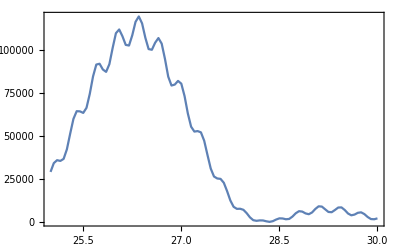

```mathematica
ListLinePlot[tk03s1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk03sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/5,0]},{x,25,30,0.05}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.564×10^7}. NIntegrate obtained 1.04561×10^6-1.5901×10^6 ⅈ and 2447.45 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.94668×10^7}. NIntegrate obtained 984701.+2.92962×10^6 ⅈ and 3053.01 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained 1.99764×10^6+288515. ⅈ and 2490.97 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained -2.28736×10^6+2.17595×10^6 ⅈ and 3104.61 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.11685×10^7}. NIntegrate obtained 613729.+2.02845×10^6 ⅈ and 2534.11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.24467×10^7}. NIntegrate obtained -2.98316×10^6-1.17288×10^6 ⅈ and 3157.49 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained -3.22092×10^6-1.134×10^6 ⅈ and 3777.4 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained -330760.-3.38506×10^6 ⅈ and 3830.85 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained 2.28804×10^6-1.47164×10^6 ⅈ and 4649.75 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained 2.90147×10^6-1.71254×10^6 ⅈ and 3886. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained 2.23146×10^6+1.40746×10^6 ⅈ and 4725.55 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained -318483.+2.52093×10^6 ⅈ and 4801.59 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.24467×10^7}. NIntegrate obtained -121612.+1.38516×10^6 ⅈ and 5678.66 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.90433×10^7}. NIntegrate obtained -1.20653×10^6+445721. ⅈ and 5767.32 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.90433×10^7}. NIntegrate obtained -837517.-818892. ⅈ and 5855.55 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained -72565.-63867.5 ⅈ and 6892.71 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.70194×10^7}. NIntegrate obtained -5873.23-25264.2 ⅈ and 6995.1 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained -62132.3-16796.4 ⅈ and 7098.7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained -155984.+573921. ⅈ and 8200.56 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained -602118.+100790. ⅈ and 8316.61 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained -641763.+138913. ⅈ and 9700.31 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14836×10^6}. NIntegrate obtained -345576.-524338. ⅈ and 8434.08 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained -386690.-497275. ⅈ and 9836.58 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.11685×10^7}. NIntegrate obtained 273865.-529950. ⅈ and 9972.22 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

(25. | 33901.6
25.05 | 35981.
25.1 | 42720.5
25.15 | 52261.6
25.2 | 60253.2
25.25 | 63543.3
25.3 | 62939.
25.35 | 63127.5
25.4 | 68271.1
25.45 | 78051.2
25.5 | 88135.9
25.55 | 93438.
25.6 | 92379.7
25.65 | 89079.4
25.7 | 89375.6
25.75 | 95689.7
25.8 | 105264.
25.85 | 111879.
25.9 | 111283.
25.95 | 105743.
26. | 101422.
26.05 | 103081.
26.1 | 110358.
26.15 | 117417.
26.2 | 118198.
26.25 | 112270.
26.3 | 104240.
26.35 | 99974.2
26.4 | 101979.
26.45 | 106637.
26.5 | 107729.
26.55 | 102241.
26.6 | 92132.3
26.65 | 83034.8
26.7 | 79628.4
26.75 | 81313.6
26.8 | 82438.8
26.85 | 79154.2
26.9 | 70605.2
26.95 | 60759.7
27. | 54563.8
27.05 | 53344.
27.1 | 54217.1
27.15 | 52983.4
27.2 | 47340.6
27.25 | 39042.2
27.3 | 31957.6
27.35 | 28491.6
27.4 | 28000.2
27.45 | 27772.4
27.5 | 25152.8
27.55 | 20002.8
27.6 | 14464.
27.65 | 10827.2
27.7 | 9756.76
27.75 | 9942.81
27.8 | 9453.77
27.85 | 7475.86
27.9 | 4722.39
27.95 | 2491.59
28. | 1519.73
28.05 | 1502.54
28.1 | 1651.12
28.15 | 1457.47
28.2 | 985.009
28.25 | 550.335
28.3 | 309.794
28.35 | 174.92
28.4 | 75.5236
28.45 | 166.041
28.5 | 668.888
28.55 | 1513.02
28.6 | 2227.16
28.65 | 2326.9
28.7 | 1824.46
28.75 | 1320.04
28.8 | 1531.4
28.85 | 2607.19
28.9 | 3888.88
28.95 | 4466.94
29. | 3936.52
29.05 | 2887.15
29.1 | 2256.96
29.15 | 2663.86
29.2 | 3806.45
29.25 | 4720.14
29.3 | 4596.16
29.35 | 3499.81
29.4 | 2270.98
29.45 | 1812.82
29.5 | 2334.71
29.55 | 3199.66
29.6 | 3516.
29.65 | 2921.18
29.7 | 1814.22
29.75 | 965.093
29.8 | 849.512
29.85 | 1302.12
29.9 | 1749.57
29.95 | 1731.58
30. | 1222.16)

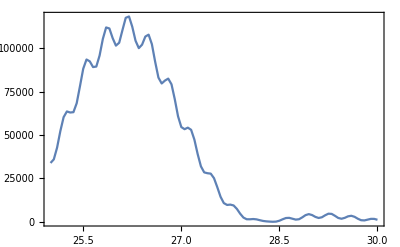

```mathematica
ListLinePlot[tk03sm1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk04s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/5,0]},{x,23.5,28.5,0.05}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14836×10^6}. NIntegrate obtained -35353.9+61168.6 ⅈ and 1811.51 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.564×10^7}. NIntegrate obtained -563671.+406660. ⅈ and 1426.75 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.3616×10^7}. NIntegrate obtained -163128.+34888.2 ⅈ and 1844.95 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.564×10^7}. NIntegrate obtained -565727.-323513. ⅈ and 1453.71 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained -177152.-189893. ⅈ and 1879.08 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.564×10^7}. NIntegrate obtained 66022.8-610855. ⅈ and 1480.99 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained -1.03391×10^6-967649. ⅈ and 2285.39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained 476197.-1.46603×10^6 ⅈ and 2323.96 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained 2.71927×10^6-464716. ⅈ and 2854.75 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.65958×10^7}. NIntegrate obtained 1.6426×10^6-211166. ⅈ and 2363.09 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained 1.62062×10^6+2.34833×10^6 ⅈ and 2903.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.11685×10^7}. NIntegrate obtained -1.48146×10^6+2.53167×10^6 ⅈ and 2952.94 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained -1.60578×10^6+3.01171×10^6 ⅈ and 3543.35 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained -3.42829×10^6-191911. ⅈ and 3598.96 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained -1.27607×10^6-3.19292×10^6 ⅈ and 3656.91 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained -1.23515×10^6-2.78266×10^6 ⅈ and 4282.38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained 1.96543×10^6-2.24283×10^6 ⅈ and 4436.74 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained 2.79498×10^6+813470. ⅈ and 4510.39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.18131×10^7}. NIntegrate obtained 1.22221×10^6-1.51074×10^6 ⅈ and 5263.6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained 1.78744×10^6+460751. ⅈ and 5343.32 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained 316188.+1.71931×10^6 ⅈ and 5425.78 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.18131×10^7}. NIntegrate obtained 626976.+131172. ⅈ and 6305.94 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.65958×10^7}. NIntegrate obtained 106949.+529690. ⅈ and 6407.02 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained -371315.+259011. ⅈ and 6499.43 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

(23.5 | 2768.69
23.55 | 3724.51
23.6 | 3861.27
23.65 | 2970.24
23.7 | 1675.76
23.75 | 836.88
23.8 | 811.375
23.85 | 1261.67
23.9 | 1566.1
23.95 | 1387.96
24. | 884.123
24.05 | 414.669
24.1 | 150.971
24.15 | 37.7345
24.2 | 62.0312
24.25 | 423.764
24.3 | 1310.
24.35 | 2517.46
24.4 | 3431.22
24.45 | 3591.8
24.5 | 3335.39
24.55 | 3745.43
24.6 | 5811.89
24.65 | 9390.7
24.7 | 12990.5
24.75 | 14955.9
24.8 | 15051.8
24.85 | 14930.4
24.9 | 17038.8
24.95 | 22358.
25. | 29128.8
25.05 | 34244.5
25.1 | 35951.5
25.15 | 35532.7
25.2 | 36716.4
25.25 | 42293.8
25.3 | 51338.6
25.35 | 59993.9
25.4 | 64511.7
25.45 | 64400.4
25.5 | 63505.
25.55 | 66472.3
25.6 | 74573.5
25.65 | 84758.5
25.7 | 91669.8
25.75 | 92152.1
25.8 | 88811.8
25.85 | 87415.1
25.9 | 91927.4
25.95 | 101370.
26. | 109949.
26.05 | 112123.
26.1 | 108146.
26.15 | 103139.
26.2 | 102769.
26.25 | 108738.
26.3 | 116574.
26.35 | 119706.
26.4 | 115666.
26.45 | 107305.
26.5 | 100699.
26.55 | 100302.
26.6 | 104415.
26.65 | 107122.
26.7 | 103857.
26.75 | 94981.1
26.8 | 84625.2
26.85 | 79460.6
26.9 | 80015.4
26.95 | 82147.3
27. | 80534.6
27.05 | 73278.3
27.1 | 63168.
27.15 | 55459.6
27.2 | 52629.9
27.25 | 52913.2
27.3 | 52175.5
27.35 | 47296.6
27.4 | 39046.4
27.45 | 31086.1
27.5 | 26446.7
27.55 | 25300.5
27.6 | 25066.
27.65 | 22804.5
27.7 | 17956.2
27.75 | 12485.8
27.8 | 8789.46
27.85 | 7598.34
27.9 | 7656.21
27.95 | 7039.31
28. | 5086.28
28.05 | 2641.54
28.1 | 1009.86
28.15 | 629.205
28.2 | 868.732
28.25 | 834.47
28.3 | 352.903
28.35 | 22.528
28.4 | 425.315
28.45 | 1366.34
28.5 | 2065.65)

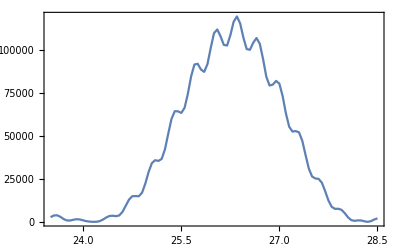

```mathematica
ListLinePlot[tk04s1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk04sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/5,0]},{x,23.5,28.5,0.05}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.29752×10^6}. NIntegrate obtained -25721.7-68658.3 ⅈ and 1811.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained 612271.-377531. ⅈ and 1426.78 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.94668×10^7}. NIntegrate obtained 126956.-73741.4 ⅈ and 1844.88 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained 586789.+383541. ⅈ and 1453.67 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained 175680.+159221. ⅈ and 1878.85 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained -84642.+661164. ⅈ and 1481.03 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained 1.08445×10^6+952159. ⅈ and 2283.84 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained -447173.+1.4784×10^6 ⅈ and 2323.54 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained -2.74437×10^6+486309. ⅈ and 2855.86 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained -1.642×10^6+213238. ⅈ and 2365.8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained -1.62514×10^6-2.34824×10^6 ⅈ and 2904.44 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained 1.50115×10^6-2.51603×10^6 ⅈ and 2953.52 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained 1.60905×10^6-3.01771×10^6 ⅈ and 3544.05 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.0745×10^7}. NIntegrate obtained 3.40832×10^6+201360. ⅈ and 3605.01 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained 1.23244×10^6+3.18132×10^6 ⅈ and 3665.47 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained 1.22813×10^6+2.76402×10^6 ⅈ and 4153.3 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained -1.93753×10^6+2.21043×10^6 ⅈ and 4436.75 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.90433×10^7}. NIntegrate obtained -2.74138×10^6-822100. ⅈ and 4503.88 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained -1.20694×10^6+1.51978×10^6 ⅈ and 5263.82 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained -1.77181×10^6-423085. ⅈ and 5348.37 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained -331823.-1.66861×10^6 ⅈ and 5429.67 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.564×10^7}. NIntegrate obtained -638837.-123593. ⅈ and 6309.78 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained -144107.-533185. ⅈ and 6392.3 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.53177×10^7}. NIntegrate obtained 334422.-294665. ⅈ and 6501.85 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

(23.5 | 6005.75
23.55 | 4053.61
23.6 | 3604.59
23.65 | 4420.54
23.7 | 5144.9
23.75 | 4648.88
23.8 | 3007.77
23.85 | 1340.71
23.9 | 654.407
23.95 | 907.671
24. | 1219.45
24.05 | 910.093
24.1 | 235.584
24.15 | 47.8898
24.2 | 756.633
24.25 | 1800.96
24.3 | 2274.56
24.35 | 2067.87
24.4 | 2201.97
24.45 | 3900.82
24.5 | 7230.42
24.55 | 10732.
24.6 | 12696.
24.65 | 12926.8
24.7 | 13176.3
24.75 | 15829.3
24.8 | 21579.5
24.85 | 28344.7
24.9 | 32991.5
24.95 | 34212.2
25. | 33901.6
25.05 | 35981.
25.1 | 42720.5
25.15 | 52261.6
25.2 | 60253.2
25.25 | 63543.3
25.3 | 62939.
25.35 | 63127.5
25.4 | 68271.1
25.45 | 78051.2
25.5 | 88135.9
25.55 | 93438.
25.6 | 92379.7
25.65 | 89079.4
25.7 | 89375.6
25.75 | 95689.7
25.8 | 105264.
25.85 | 111879.
25.9 | 111283.
25.95 | 105743.
26. | 101422.
26.05 | 103081.
26.1 | 110358.
26.15 | 117417.
26.2 | 118198.
26.25 | 112270.
26.3 | 104240.
26.35 | 99974.2
26.4 | 101979.
26.45 | 106637.
26.5 | 107729.
26.55 | 102241.
26.6 | 92132.3
26.65 | 83034.8
26.7 | 79628.4
26.75 | 81313.6
26.8 | 82438.8
26.85 | 79154.2
26.9 | 70605.2
26.95 | 60759.7
27. | 54563.8
27.05 | 53344.
27.1 | 54217.1
27.15 | 52983.4
27.2 | 47340.6
27.25 | 39042.2
27.3 | 31957.6
27.35 | 28491.6
27.4 | 28000.2
27.45 | 27772.4
27.5 | 25152.8
27.55 | 20002.8
27.6 | 14464.
27.65 | 10827.2
27.7 | 9756.76
27.75 | 9942.81
27.8 | 9453.77
27.85 | 7475.86
27.9 | 4722.39
27.95 | 2491.59
28. | 1519.73
28.05 | 1502.54
28.1 | 1651.12
28.15 | 1457.47
28.2 | 985.009
28.25 | 550.335
28.3 | 309.794
28.35 | 174.92
28.4 | 75.5236
28.45 | 166.041
28.5 | 668.888)

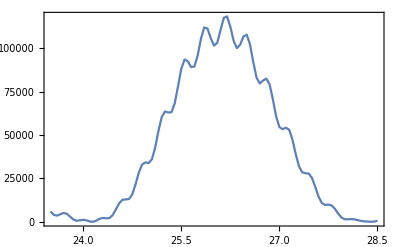

```mathematica
ListLinePlot[tk04sm1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
llt2s1=AmplTwistTab[1,26.3/mee,26.3/mee/5];
llt2sm1=AmplTwistTab[-1,26.3/mee,26.3/mee/5];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.9227×10^7}. NIntegrate obtained 3.22694×10^6+1.0702×10^6 ⅈ and 3878.99 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained 3.22491×10^6+1.08179×10^6 ⅈ and 3785.79 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.75254×10^7}. NIntegrate obtained 3.22743×10^6+1.07164×10^6 ⅈ and 3887.39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained 3.22465×10^6+1.07938×10^6 ⅈ and 3781.78 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.37997×10^7}. NIntegrate obtained 3.22794×10^6+1.07331×10^6 ⅈ and 3894.51 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.98904×10^7}. NIntegrate obtained 3.22444×10^6+1.07712×10^6 ⅈ and 3777.97 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.13637×10^6}. NIntegrate obtained 3.23427×10^6+1.10824×10^6 ⅈ and 3936.68 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.11238×10^6}. NIntegrate obtained 3.23449×10^6+1.11062×10^6 ⅈ and 3939.77 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.92832×10^7}. NIntegrate obtained 3.23207×10^6+1.12038×10^6 ⅈ and 3844.96 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.23757×10^6}. NIntegrate obtained 3.23466×10^6+1.11286×10^6 ⅈ and 3943.07 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.61838×10^6}. NIntegrate obtained 3.23162×10^6+1.11898×10^6 ⅈ and 3836.75 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.61838×10^6}. NIntegrate obtained 3.23115×10^6+1.11734×10^6 ⅈ and 3829.83 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained 3.2249×10^6+1.08179×10^6 ⅈ and 3785.79 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained 3.22464×10^6+1.07938×10^6 ⅈ and 3781.78 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.98904×10^7}. NIntegrate obtained 3.22443×10^6+1.07712×10^6 ⅈ and 3777.97 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.9227×10^7}. NIntegrate obtained 3.22693×10^6+1.0702×10^6 ⅈ and 3878.99 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.75254×10^7}. NIntegrate obtained 3.22742×10^6+1.07164×10^6 ⅈ and 3887.39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.37997×10^7}. NIntegrate obtained 3.22793×10^6+1.07331×10^6 ⅈ and 3894.51 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.13637×10^6}. NIntegrate obtained 3.23426×10^6+1.10824×10^6 ⅈ and 3936.68 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.11238×10^6}. NIntegrate obtained 3.23447×10^6+1.11061×10^6 ⅈ and 3939.77 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.92832×10^7}. NIntegrate obtained 3.23207×10^6+1.12038×10^6 ⅈ and 3844.96 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.23757×10^6}. NIntegrate obtained 3.23464×10^6+1.11285×10^6 ⅈ and 3943.07 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.61838×10^6}. NIntegrate obtained 3.23162×10^6+1.11898×10^6 ⅈ and 3836.75 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.61838×10^6}. NIntegrate obtained 3.23115×10^6+1.11734×10^6 ⅈ and 3829.83 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained -3.22092×10^6-1.134×10^6 ⅈ and 3777.4 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.02951×10^7}. NIntegrate obtained 1.16066×10^6-3.22565×10^6 ⅈ and 3846.02 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {100394.}. NIntegrate obtained -3.09379×10^6-1.44775×10^6 ⅈ and 3782.79 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {606389.}. NIntegrate obtained 1.47018×10^6-3.09711×10^6 ⅈ and 3852.68 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {100394.}. NIntegrate obtained -2.93627×10^6-1.74735×10^6 ⅈ and 3788.09 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {606389.}. NIntegrate obtained 1.76537×10^6-2.93902×10^6 ⅈ and 3860.68 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.87772×10^7}. NIntegrate obtained 3.23377×10^6+1.11519×10^6 ⅈ and 3944.59 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.09023×10^7}. NIntegrate obtained 3.10934×10^6+1.42333×10^6 ⅈ and 3940.21 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.43882×10^7}. NIntegrate obtained -1.08824×10^6+3.22872×10^6 ⅈ and 3879.69 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.09023×10^7}. NIntegrate obtained 2.95555×10^6+1.71795×10^6 ⅈ and 3935.38 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.65134×10^7}. NIntegrate obtained -1.40048×10^6+3.10577×10^6 ⅈ and 3871.89 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.48117×10^7}. NIntegrate obtained -1.69942×10^6+2.95264×10^6 ⅈ and 3862.6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained -3.22092×10^6-1.13401×10^6 ⅈ and 3777.4 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {100394.}. NIntegrate obtained -3.0938×10^6-1.44775×10^6 ⅈ and 3782.79 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {100394.}. NIntegrate obtained -2.93628×10^6-1.74735×10^6 ⅈ and 3788.09 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.02951×10^7}. NIntegrate obtained 1.16066×10^6-3.22565×10^6 ⅈ and 3846.02 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {606389.}. NIntegrate obtained 1.47018×10^6-3.0971×10^6 ⅈ and 3852.68 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {606389.}. NIntegrate obtained 1.76536×10^6-2.93901×10^6 ⅈ and 3860.68 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.87772×10^7}. NIntegrate obtained 3.23375×10^6+1.11518×10^6 ⅈ and 3944.59 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.09023×10^7}. NIntegrate obtained 3.10932×10^6+1.42332×10^6 ⅈ and 3940.21 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.43882×10^7}. NIntegrate obtained -1.08823×10^6+3.22871×10^6 ⅈ and 3879.69 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.09023×10^7}. NIntegrate obtained 2.95554×10^6+1.71794×10^6 ⅈ and 3935.38 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.65134×10^7}. NIntegrate obtained -1.40047×10^6+3.10576×10^6 ⅈ and 3871.89 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.48117×10^7}. NIntegrate obtained -1.69941×10^6+2.95263×10^6 ⅈ and 3862.6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
tm2s1=Table[{m,dProbabTwist[m,llt2s1[[3]]]},{m,-mMax,mMax}];
tm2sm1=Table[{m,dProbabTwist[m,llt2sm1[[3]]]},{m,-mMax,mMax}];
```

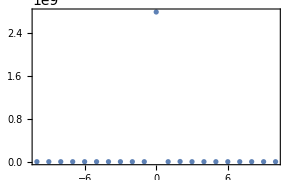
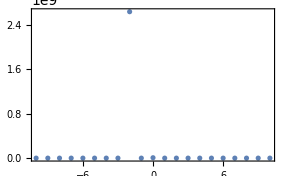

```mathematica
{ListPlot[tm2s1,Frame->True,Axes->False,PlotRange->Full],ListPlot[tm2sm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
tk0=ParallelTable[{x,dProbabPlane[-1,x/mee,1/γ,0]},{x,0.01,1,0.01/4}](*ТВ не работает в окрестности щели*)
tk0m1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/γ,0]},{x,0.01,1,0.01/4}]
```

(0.01 | 5.47105×10^6
0.0125 | 6.60793×10^6
0.015 | 7.72229×10^6
0.0175 | 8.87571×10^6
0.02 | 1.01152×10^7
0.0225 | 1.14574×10^7
0.025 | 1.28813×10^7
0.0275 | 1.43338×10^7
0.03 | 1.57484×10^7
0.0325 | 1.70693×10^7
0.035 | 1.82716×10^7
0.0375 | 1.93683×10^7
0.04 | 2.04041×10^7
0.0425 | 2.1439×10^7
0.045 | 2.25287×10^7
0.0475 | 2.37065×10^7
0.05 | 2.49711×10^7
0.0525 | 2.6286×10^7
0.055 | 2.75904×10^7
0.0575 | 2.88213×10^7
0.06 | 2.99364×10^7
0.0625 | 3.09289×10^7
0.065 | 3.18281×10^7
0.0675 | 3.26878×10^7
0.07 | 3.35673×10^7
0.0725 | 3.45122×10^7
0.075 | 3.55396×10^7
0.0775 | 3.66315×10^7
0.08 | 3.77392×10^7
0.0825 | 3.87999×10^7
0.085 | 3.97591×10^7
0.0875 | 4.05911×10^7
0.09 | 4.13072×10^7
0.0925 | 4.19496×10^7
0.095 | 4.25763×10^7
0.0975 | 4.32408×10^7
0.1 | 4.39754×10^7
0.1025 | 4.47803×10^7
0.105 | 4.56227×10^7
0.1075 | 4.64467×10^7
0.11 | 4.71926×10^7
0.1125 | 4.78191×10^7
0.115 | 4.83183×10^7
0.1175 | 4.87174×10^7
0.12 | 4.90678×10^7
0.1225 | 4.94261×10^7
0.125 | 4.98362×10^7
0.1275 | 5.0315×10^7
0.13 | 5.0847×10^7
0.1325 | 5.13881×10^7
0.135 | 5.18801×10^7
0.1375 | 5.22715×10^7
0.14 | 5.25366×10^7
0.1425 | 5.26848×10^7
0.145 | 5.27561×10^7
0.1475 | 5.28055×10^7
0.15 | 5.28845×10^7
0.1525 | 5.30242×10^7
0.155 | 5.3226×10^7
0.1575 | 5.3461×10^7
0.16 | 5.36783×10^7
0.1625 | 5.38227×10^7
0.165 | 5.38542×10^7
0.1675 | 5.37635×10^7
0.17 | 5.35751×10^7
0.1725 | 5.3337×10^7
0.175 | 5.31035×10^7
0.1775 | 5.29169×10^7
0.18 | 5.27945×10^7
0.1825 | 5.27237×10^7
0.185 | 5.26658×10^7
0.1875 | 5.25682×10^7
0.19 | 5.23824×10^7
0.1925 | 5.20823×10^7
0.195 | 5.16739×10^7
0.1975 | 5.11929×10^7
0.2 | 5.06908×10^7
0.2025 | 5.02163×10^7
0.205 | 4.98006×10^7
0.2075 | 4.94475×10^7
0.21 | 4.91333×10^7
0.2125 | 4.88139×10^7
0.215 | 4.84393×10^7
0.2175 | 4.79711×10^7
0.22 | 4.73974×10^7
0.2225 | 4.67368×10^7
0.225 | 4.60317×10^7
0.2275 | 4.53318×10^7
0.23 | 4.46776×10^7
0.2325 | 4.40878×10^7
0.235 | 4.35549×10^7
0.2375 | 4.30476×10^7
0.24 | 4.25211×10^7
0.2425 | 4.1932×10^7
0.245 | 4.12537×10^7
0.2475 | 4.0487×10^7
0.25 | 3.96594×10^7
0.2525 | 3.8815×10^7
0.255 | 3.79977×10^7
0.2575 | 3.72375×10^7
0.26 | 3.65415×10^7
0.2625 | 3.58935×10^7
0.265 | 3.52592×10^7
0.2675 | 3.45972×10^7
0.27 | 3.38734×10^7
0.2725 | 3.30733×10^7
0.275 | 3.22077×10^7
0.2775 | 3.13086×10^7
0.28 | 3.0417×10^7
0.2825 | 2.95681×10^7
0.285 | 2.87805×10^7
0.2875 | 2.8052×10^7
0.29 | 2.7361×10^7
0.2925 | 2.66743×10^7
0.295 | 2.59576×10^7
0.2975 | 2.51876×10^7
0.3 | 2.43603×10^7
0.3025 | 2.34933×10^7
0.305 | 2.26183×10^7
0.3075 | 2.17695×10^7
0.31 | 2.09715×10^7
0.3125 | 2.02325×10^7
0.315 | 1.95434×10^7
0.3175 | 1.88815×10^7
0.32 | 1.82182×10^7
0.3225 | 1.75286×10^7
0.325 | 1.67999×10^7
0.3275 | 1.60367×10^7
0.33 | 1.52589×10^7
0.3325 | 1.44941×10^7
0.335 | 1.37668×10^7
0.3375 | 1.30909×10^7
0.34 | 1.24663×10^7
0.3425 | 1.18802×10^7
0.345 | 1.13124×10^7
0.3475 | 1.0742×10^7
0.35 | 1.01539×10^7
0.3525 | 9.54491×10^6
0.355 | 8.92433×10^6
0.3575 | 8.3106×10^6
0.36 | 7.72364×10^6
0.3625 | 7.17763×10^6
0.365 | 6.6769×10^6
0.3675 | 6.21592×10^6
0.37 | 5.78228×10^6
0.3725 | 5.3612×10^6
0.375 | 4.94049×10^6
0.3775 | 4.51459×10^6
0.38 | 4.08658×10^6
0.3825 | 3.66676×10^6
0.385 | 3.26827×10^6
0.3875 | 2.90174×10^6
0.39 | 2.57171×10^6
0.3925 | 2.27602×10^6
0.395 | 2.0077×10^6
0.3975 | 1.75802×10^6
0.4 | 1.51959×10^6
0.4025 | 1.28872×10^6
0.405 | 1.06658×10^6
0.4075 | 858385.
0.41 | 670910.
0.4125 | 509393.
0.415 | 375509.
0.4175 | 267331.
0.42 | 180890.
0.4225 | 112249.
0.425 | 59150.1
0.4275 | 21741.4
0.43 | 2199.14
0.4325 | 3323.26
0.435 | 26681.7
0.4375 | 71355.9
0.44 | 134186.
0.4425 | 211432.
0.445 | 300831.
0.4475 | 402944.
0.45 | 521293.
0.4525 | 661224.
0.455 | 827663.
0.4575 | 1.02225×10^6
0.46 | 1.24112×10^6
0.4625 | 1.47518×10^6
0.465 | 1.71358×10^6
0.4675 | 1.94881×10^6
0.47 | 2.1804×10^6
0.4725 | 2.41549×10^6
0.475 | 2.6665×10^6
0.4775 | 2.94721×10^6
0.48 | 3.26781×10^6
0.4825 | 3.62954×10^6
0.485 | 4.02088×10^6
0.4875 | 4.41888×10^6
0.49 | 4.79782×10^6
0.4925 | 5.14168×10^6
0.495 | 5.45243×10^6
0.4975 | 5.7493×10^6
0.5 | 6.06137×10^6
0.5025 | 6.41824×10^6
0.505 | 6.84082×10^6
0.5075 | 7.33195×10^6
0.51 | 7.86875×10^6
0.5125 | 8.40329×10^6
0.515 | 8.87932×10^6
0.5175 | 9.26082×10^6
0.52 | 9.55277×10^6
0.5225 | 9.79841×10^6
0.525 | 1.00594×10^7
0.5275 | 1.03949×10^7
0.53 | 1.08453×10^7
0.5325 | 1.14176×10^7
0.535 | 1.20708×10^7
0.5375 | 1.27108×10^7
0.54 | 1.32193×10^7
0.5425 | 1.35194×10^7
0.545 | 1.36274×10^7
0.5475 | 1.36423×10^7
0.55 | 1.36915×10^7
0.5525 | 1.38831×10^7
0.555 | 1.42828×10^7
0.5575 | 1.48966×10^7
0.56 | 1.56399×10^7
0.5625 | 1.63168×10^7
0.565 | 1.66796×10^7
0.5675 | 1.65975×10^7
0.57 | 1.61768×10^7
0.5725 | 1.56762×10^7
0.575 | 1.53394×10^7
0.5775 | 1.53181×10^7
0.58 | 1.56721×10^7
0.5825 | 1.63488×10^7
0.585 | 1.70933×10^7
0.5875 | 1.73893×10^7
0.59 | 1.67709×10^7
0.5925 | 1.53986×10^7
0.595 | 1.39306×10^7
0.5975 | 1.28704×10^7
0.6 | 1.23869×10^7
0.6025 | 1.2472×10^7
0.605 | 1.297×10^7
0.6075 | 1.32247×10^7
0.61 | 1.17782×10^7
0.6125 | 8.62599×10^6
0.615 | 6.07616×10^6
0.6175 | 4.82199×10^6
0.62 | 4.33751×10^6
0.6225 | 4.10685×10^6
0.625 | 2.75502×10^6
0.6275 | 126421.
0.63 | 1.53246×10^6
0.6325 | 1.03692×10^7
0.635 | 8.18523×10^6
0.6375 | 7.82378×10^6
0.64 | 7.74341×10^6
0.6425 | 7.73719×10^6
0.645 | 7.7519×10^6
0.6475 | 7.77022×10^6
0.65 | 7.78607×10^6
0.6525 | 7.79737×10^6
0.655 | 7.80365×10^6
0.6575 | 7.80508×10^6
0.66 | 7.80205×10^6
0.6625 | 7.795×10^6
0.665 | 7.78438×10^6
0.6675 | 7.7706×10^6
0.67 | 7.75402×10^6
0.6725 | 7.73494×10^6
0.675 | 7.71362×10^6
0.6775 | 7.69028×10^6
0.68 | 7.66512×10^6
0.6825 | 7.63829×10^6
0.685 | 7.60991×10^6
0.6875 | 7.58009×10^6
0.69 | 7.54894×10^6
0.6925 | 7.51652×10^6
0.695 | 7.48291×10^6
0.6975 | 7.4482×10^6
0.7 | 7.41247×10^6
0.7025 | 7.37584×10^6
0.705 | 7.33847×10^6
0.7075 | 7.30061×10^6
0.71 | 7.26262×10^6
0.7125 | 7.22508×10^6
0.715 | 7.18893×10^6
0.7175 | 7.15567×10^6
0.72 | 7.12784×10^6
0.7225 | 7.10983×10^6
0.725 | 7.10961×10^6
0.7275 | 7.14259×10^6
0.73 | 7.24142×10^6
0.7325 | 7.48521×10^6
0.735 | 8.11365×10^6
0.7375 | 1.02633×10^7
0.74 | 3.39193×10^6
0.7425 | 3.07702×10^6
0.745 | 359770.
0.7475 | 770360.
0.75 | 1.32971×10^6
0.7525 | 1.38×10^6
0.755 | 1.3122×10^6
0.7575 | 1.54197×10^6
0.76 | 2.8509×10^6
0.7625 | 5.00809×10^6
0.765 | 6.15393×10^6
0.7675 | 6.3214×10^6
0.77 | 6.25453×10^6
0.7725 | 6.28534×10^6
0.775 | 6.57143×10^6
0.7775 | 7.24602×10^6
0.78 | 8.34754×10^6
0.7825 | 9.56486×10^6
0.785 | 1.03149×10^7
0.7875 | 1.04297×10^7
0.79 | 1.02306×10^7
0.7925 | 1.00315×10^7
0.795 | 9.98407×10^6
0.7975 | 1.01438×10^7
0.8 | 1.05137×10^7
0.8025 | 1.10261×10^7
0.805 | 1.15085×10^7
0.8075 | 1.17433×10^7
0.81 | 1.16515×10^7
0.8125 | 1.13595×10^7
0.815 | 1.10512×10^7
0.8175 | 1.08422×10^7
0.82 | 1.07715×10^7
0.8225 | 1.08284×10^7
0.825 | 1.09652×10^7
0.8275 | 1.10965×10^7
0.83 | 1.11152×10^7
0.8325 | 1.09495×10^7
0.835 | 1.06238×10^7
0.8375 | 1.02415×10^7
0.84 | 9.90626×10^6
0.8425 | 9.67112×10^6
0.845 | 9.53966×10^6
0.8475 | 9.48293×10^6
0.85 | 9.45058×10^6
0.8525 | 9.37853×10^6
0.855 | 9.20635×10^6
0.8575 | 8.90911×10^6
0.86 | 8.52115×10^6
0.8625 | 8.11881×10^6
0.865 | 7.77275×10^6
0.8675 | 7.51588×10^6
0.87 | 7.34305×10^6
0.8725 | 7.22451×10^6
0.875 | 7.11748×10^6
0.8775 | 6.97487×10^6
0.88 | 6.75733×10^6
0.8825 | 6.45118×10^6
0.885 | 6.08144×10^6
0.8875 | 5.70279×10^6
0.89 | 5.3697×10^6
0.8925 | 5.11073×10^6
0.895 | 4.92385×10^6
0.8975 | 4.78582×10^6
0.9 | 4.66324×10^6
0.9025 | 4.52097×10^6
0.905 | 4.33018×10^6
0.9075 | 4.07842×10^6
0.91 | 3.77806×10^6
0.9125 | 3.46385×10^6
0.915 | 3.17646×10^6
0.9175 | 2.94287×10^6
0.92 | 2.7678×10^6
0.9225 | 2.63772×10^6
0.925 | 2.52958×10^6
0.9275 | 2.41837×10^6
0.93 | 2.28301×10^6
0.9325 | 2.1119×10^6
0.935 | 1.90781×10^6
0.9375 | 1.68844×10^6
0.94 | 1.47933×10^6
0.9425 | 1.30185×10^6
0.945 | 1.16468×10^6
0.9475 | 1.06325×10^6
0.95 | 984746.
0.9525 | 913918.
0.955 | 837427.
0.9575 | 746935.
0.96 | 641302.
0.9625 | 527115.
0.965 | 416164.
0.9675 | 320129.
0.97 | 245505.
0.9725 | 191960.
0.975 | 154291.
0.9775 | 125739.
0.98 | 100693.
0.9825 | 76189.5
0.985 | 52326.
0.9875 | 31656.
0.99 | 17622.2
0.9925 | 12540.6
0.995 | 16287.7
0.9975 | 26584.7
1. | 40575.9)

(0.01 | 5.47105×10^6
0.0125 | 6.60793×10^6
0.015 | 7.72229×10^6
0.0175 | 8.87571×10^6
0.02 | 1.01152×10^7
0.0225 | 1.14574×10^7
0.025 | 1.28813×10^7
0.0275 | 1.43338×10^7
0.03 | 1.57484×10^7
0.0325 | 1.70693×10^7
0.035 | 1.82716×10^7
0.0375 | 1.93683×10^7
0.04 | 2.04041×10^7
0.0425 | 2.1439×10^7
0.045 | 2.25287×10^7
0.0475 | 2.37065×10^7
0.05 | 2.49711×10^7
0.0525 | 2.6286×10^7
0.055 | 2.75904×10^7
0.0575 | 2.88213×10^7
0.06 | 2.99364×10^7
0.0625 | 3.09289×10^7
0.065 | 3.18281×10^7
0.0675 | 3.26878×10^7
0.07 | 3.35673×10^7
0.0725 | 3.45122×10^7
0.075 | 3.55396×10^7
0.0775 | 3.66315×10^7
0.08 | 3.77392×10^7
0.0825 | 3.87999×10^7
0.085 | 3.97591×10^7
0.0875 | 4.05911×10^7
0.09 | 4.13072×10^7
0.0925 | 4.19496×10^7
0.095 | 4.25763×10^7
0.0975 | 4.32408×10^7
0.1 | 4.39754×10^7
0.1025 | 4.47803×10^7
0.105 | 4.56227×10^7
0.1075 | 4.64467×10^7
0.11 | 4.71926×10^7
0.1125 | 4.78191×10^7
0.115 | 4.83183×10^7
0.1175 | 4.87174×10^7
0.12 | 4.90678×10^7
0.1225 | 4.94261×10^7
0.125 | 4.98362×10^7
0.1275 | 5.0315×10^7
0.13 | 5.0847×10^7
0.1325 | 5.13881×10^7
0.135 | 5.18801×10^7
0.1375 | 5.22715×10^7
0.14 | 5.25366×10^7
0.1425 | 5.26848×10^7
0.145 | 5.27561×10^7
0.1475 | 5.28055×10^7
0.15 | 5.28845×10^7
0.1525 | 5.30242×10^7
0.155 | 5.3226×10^7
0.1575 | 5.3461×10^7
0.16 | 5.36783×10^7
0.1625 | 5.38227×10^7
0.165 | 5.38542×10^7
0.1675 | 5.37635×10^7
0.17 | 5.35751×10^7
0.1725 | 5.3337×10^7
0.175 | 5.31035×10^7
0.1775 | 5.29169×10^7
0.18 | 5.27945×10^7
0.1825 | 5.27237×10^7
0.185 | 5.26658×10^7
0.1875 | 5.25682×10^7
0.19 | 5.23824×10^7
0.1925 | 5.20823×10^7
0.195 | 5.16739×10^7
0.1975 | 5.11929×10^7
0.2 | 5.06908×10^7
0.2025 | 5.02163×10^7
0.205 | 4.98006×10^7
0.2075 | 4.94475×10^7
0.21 | 4.91333×10^7
0.2125 | 4.88139×10^7
0.215 | 4.84393×10^7
0.2175 | 4.79711×10^7
0.22 | 4.73974×10^7
0.2225 | 4.67368×10^7
0.225 | 4.60317×10^7
0.2275 | 4.53318×10^7
0.23 | 4.46776×10^7
0.2325 | 4.40878×10^7
0.235 | 4.35549×10^7
0.2375 | 4.30476×10^7
0.24 | 4.25211×10^7
0.2425 | 4.1932×10^7
0.245 | 4.12537×10^7
0.2475 | 4.0487×10^7
0.25 | 3.96594×10^7
0.2525 | 3.8815×10^7
0.255 | 3.79977×10^7
0.2575 | 3.72375×10^7
0.26 | 3.65415×10^7
0.2625 | 3.58935×10^7
0.265 | 3.52592×10^7
0.2675 | 3.45972×10^7
0.27 | 3.38734×10^7
0.2725 | 3.30733×10^7
0.275 | 3.22077×10^7
0.2775 | 3.13086×10^7
0.28 | 3.0417×10^7
0.2825 | 2.95681×10^7
0.285 | 2.87805×10^7
0.2875 | 2.8052×10^7
0.29 | 2.7361×10^7
0.2925 | 2.66743×10^7
0.295 | 2.59576×10^7
0.2975 | 2.51876×10^7
0.3 | 2.43603×10^7
0.3025 | 2.34933×10^7
0.305 | 2.26183×10^7
0.3075 | 2.17695×10^7
0.31 | 2.09715×10^7
0.3125 | 2.02325×10^7
0.315 | 1.95434×10^7
0.3175 | 1.88815×10^7
0.32 | 1.82182×10^7
0.3225 | 1.75286×10^7
0.325 | 1.67999×10^7
0.3275 | 1.60367×10^7
0.33 | 1.52589×10^7
0.3325 | 1.44941×10^7
0.335 | 1.37668×10^7
0.3375 | 1.30909×10^7
0.34 | 1.24663×10^7
0.3425 | 1.18802×10^7
0.345 | 1.13124×10^7
0.3475 | 1.0742×10^7
0.35 | 1.01539×10^7
0.3525 | 9.54491×10^6
0.355 | 8.92433×10^6
0.3575 | 8.3106×10^6
0.36 | 7.72364×10^6
0.3625 | 7.17763×10^6
0.365 | 6.6769×10^6
0.3675 | 6.21592×10^6
0.37 | 5.78228×10^6
0.3725 | 5.3612×10^6
0.375 | 4.94049×10^6
0.3775 | 4.51459×10^6
0.38 | 4.08658×10^6
0.3825 | 3.66676×10^6
0.385 | 3.26827×10^6
0.3875 | 2.90174×10^6
0.39 | 2.57171×10^6
0.3925 | 2.27602×10^6
0.395 | 2.0077×10^6
0.3975 | 1.75802×10^6
0.4 | 1.51959×10^6
0.4025 | 1.28872×10^6
0.405 | 1.06658×10^6
0.4075 | 858385.
0.41 | 670910.
0.4125 | 509393.
0.415 | 375509.
0.4175 | 267331.
0.42 | 180890.
0.4225 | 112249.
0.425 | 59150.1
0.4275 | 21741.4
0.43 | 2199.14
0.4325 | 3323.26
0.435 | 26681.7
0.4375 | 71355.9
0.44 | 134186.
0.4425 | 211432.
0.445 | 300831.
0.4475 | 402944.
0.45 | 521293.
0.4525 | 661224.
0.455 | 827663.
0.4575 | 1.02225×10^6
0.46 | 1.24112×10^6
0.4625 | 1.47518×10^6
0.465 | 1.71358×10^6
0.4675 | 1.94881×10^6
0.47 | 2.1804×10^6
0.4725 | 2.41549×10^6
0.475 | 2.6665×10^6
0.4775 | 2.94721×10^6
0.48 | 3.26781×10^6
0.4825 | 3.62954×10^6
0.485 | 4.02088×10^6
0.4875 | 4.41888×10^6
0.49 | 4.79782×10^6
0.4925 | 5.14168×10^6
0.495 | 5.45243×10^6
0.4975 | 5.7493×10^6
0.5 | 6.06137×10^6
0.5025 | 6.41824×10^6
0.505 | 6.84082×10^6
0.5075 | 7.33195×10^6
0.51 | 7.86875×10^6
0.5125 | 8.40329×10^6
0.515 | 8.87932×10^6
0.5175 | 9.26082×10^6
0.52 | 9.55277×10^6
0.5225 | 9.79841×10^6
0.525 | 1.00594×10^7
0.5275 | 1.03949×10^7
0.53 | 1.08453×10^7
0.5325 | 1.14176×10^7
0.535 | 1.20708×10^7
0.5375 | 1.27108×10^7
0.54 | 1.32193×10^7
0.5425 | 1.35194×10^7
0.545 | 1.36274×10^7
0.5475 | 1.36423×10^7
0.55 | 1.36915×10^7
0.5525 | 1.38831×10^7
0.555 | 1.42828×10^7
0.5575 | 1.48966×10^7
0.56 | 1.56399×10^7
0.5625 | 1.63168×10^7
0.565 | 1.66796×10^7
0.5675 | 1.65975×10^7
0.57 | 1.61768×10^7
0.5725 | 1.56762×10^7
0.575 | 1.53394×10^7
0.5775 | 1.53181×10^7
0.58 | 1.56721×10^7
0.5825 | 1.63488×10^7
0.585 | 1.70933×10^7
0.5875 | 1.73893×10^7
0.59 | 1.67709×10^7
0.5925 | 1.53986×10^7
0.595 | 1.39306×10^7
0.5975 | 1.28704×10^7
0.6 | 1.23869×10^7
0.6025 | 1.2472×10^7
0.605 | 1.297×10^7
0.6075 | 1.32247×10^7
0.61 | 1.17782×10^7
0.6125 | 8.62599×10^6
0.615 | 6.07616×10^6
0.6175 | 4.82199×10^6
0.62 | 4.33751×10^6
0.6225 | 4.10685×10^6
0.625 | 2.75502×10^6
0.6275 | 126421.
0.63 | 1.53246×10^6
0.6325 | 1.03692×10^7
0.635 | 8.18523×10^6
0.6375 | 7.82378×10^6
0.64 | 7.74341×10^6
0.6425 | 7.73719×10^6
0.645 | 7.7519×10^6
0.6475 | 7.77022×10^6
0.65 | 7.78607×10^6
0.6525 | 7.79737×10^6
0.655 | 7.80365×10^6
0.6575 | 7.80508×10^6
0.66 | 7.80205×10^6
0.6625 | 7.795×10^6
0.665 | 7.78438×10^6
0.6675 | 7.7706×10^6
0.67 | 7.75402×10^6
0.6725 | 7.73494×10^6
0.675 | 7.71362×10^6
0.6775 | 7.69028×10^6
0.68 | 7.66512×10^6
0.6825 | 7.63829×10^6
0.685 | 7.60991×10^6
0.6875 | 7.58009×10^6
0.69 | 7.54894×10^6
0.6925 | 7.51652×10^6
0.695 | 7.48291×10^6
0.6975 | 7.4482×10^6
0.7 | 7.41247×10^6
0.7025 | 7.37584×10^6
0.705 | 7.33847×10^6
0.7075 | 7.30061×10^6
0.71 | 7.26262×10^6
0.7125 | 7.22508×10^6
0.715 | 7.18893×10^6
0.7175 | 7.15567×10^6
0.72 | 7.12784×10^6
0.7225 | 7.10983×10^6
0.725 | 7.10961×10^6
0.7275 | 7.14259×10^6
0.73 | 7.24142×10^6
0.7325 | 7.48521×10^6
0.735 | 8.11365×10^6
0.7375 | 1.02633×10^7
0.74 | 3.39193×10^6
0.7425 | 3.07702×10^6
0.745 | 359770.
0.7475 | 770360.
0.75 | 1.32971×10^6
0.7525 | 1.38×10^6
0.755 | 1.3122×10^6
0.7575 | 1.54197×10^6
0.76 | 2.8509×10^6
0.7625 | 5.00809×10^6
0.765 | 6.15393×10^6
0.7675 | 6.3214×10^6
0.77 | 6.25453×10^6
0.7725 | 6.28534×10^6
0.775 | 6.57143×10^6
0.7775 | 7.24602×10^6
0.78 | 8.34754×10^6
0.7825 | 9.56486×10^6
0.785 | 1.03149×10^7
0.7875 | 1.04297×10^7
0.79 | 1.02306×10^7
0.7925 | 1.00315×10^7
0.795 | 9.98407×10^6
0.7975 | 1.01438×10^7
0.8 | 1.05137×10^7
0.8025 | 1.10261×10^7
0.805 | 1.15085×10^7
0.8075 | 1.17433×10^7
0.81 | 1.16515×10^7
0.8125 | 1.13595×10^7
0.815 | 1.10512×10^7
0.8175 | 1.08422×10^7
0.82 | 1.07715×10^7
0.8225 | 1.08284×10^7
0.825 | 1.09652×10^7
0.8275 | 1.10965×10^7
0.83 | 1.11152×10^7
0.8325 | 1.09495×10^7
0.835 | 1.06238×10^7
0.8375 | 1.02415×10^7
0.84 | 9.90626×10^6
0.8425 | 9.67112×10^6
0.845 | 9.53966×10^6
0.8475 | 9.48293×10^6
0.85 | 9.45058×10^6
0.8525 | 9.37853×10^6
0.855 | 9.20635×10^6
0.8575 | 8.90911×10^6
0.86 | 8.52115×10^6
0.8625 | 8.11881×10^6
0.865 | 7.77275×10^6
0.8675 | 7.51588×10^6
0.87 | 7.34305×10^6
0.8725 | 7.22451×10^6
0.875 | 7.11748×10^6
0.8775 | 6.97487×10^6
0.88 | 6.75733×10^6
0.8825 | 6.45118×10^6
0.885 | 6.08144×10^6
0.8875 | 5.70279×10^6
0.89 | 5.3697×10^6
0.8925 | 5.11073×10^6
0.895 | 4.92385×10^6
0.8975 | 4.78582×10^6
0.9 | 4.66324×10^6
0.9025 | 4.52097×10^6
0.905 | 4.33018×10^6
0.9075 | 4.07842×10^6
0.91 | 3.77806×10^6
0.9125 | 3.46385×10^6
0.915 | 3.17646×10^6
0.9175 | 2.94287×10^6
0.92 | 2.7678×10^6
0.9225 | 2.63772×10^6
0.925 | 2.52958×10^6
0.9275 | 2.41837×10^6
0.93 | 2.28301×10^6
0.9325 | 2.1119×10^6
0.935 | 1.90781×10^6
0.9375 | 1.68844×10^6
0.94 | 1.47933×10^6
0.9425 | 1.30185×10^6
0.945 | 1.16468×10^6
0.9475 | 1.06325×10^6
0.95 | 984746.
0.9525 | 913918.
0.955 | 837427.
0.9575 | 746935.
0.96 | 641302.
0.9625 | 527115.
0.965 | 416164.
0.9675 | 320129.
0.97 | 245505.
0.9725 | 191960.
0.975 | 154291.
0.9775 | 125739.
0.98 | 100693.
0.9825 | 76189.5
0.985 | 52326.
0.9875 | 31656.
0.99 | 17622.2
0.9925 | 12540.6
0.995 | 16287.7
0.9975 | 26584.7
1. | 40575.9)

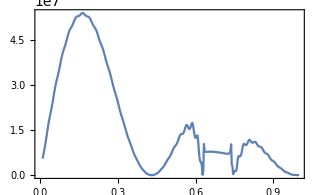
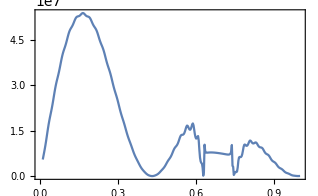

```mathematica
{ListLinePlot[tk0,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[tk0m1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
tk02=ParallelTable[{x,dProbabPlane[1,x/mee,1/γ,0]},{x,11,18,0.1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained 332.434+464.367 ⅈ and 0.0225361 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.24467×10^7}. NIntegrate obtained -619.429-681.286 ⅈ and 0.0489122 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained 1166.92-1085.18 ⅈ and 0.0531897 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained -1049.87+942.244 ⅈ and 0.0246899 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.11685×10^7}. NIntegrate obtained 1403.62+442.504 ⅈ and 0.0574778 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.18131×10^7}. NIntegrate obtained -1526.59-450.397 ⅈ and 0.0268764 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained 1065.22+1179.94 ⅈ and 0.100125 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained -1599.05-1893.63 ⅈ and 0.194516 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained -1491.3+1330.95 ⅈ and 0.107954 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained 1990.87-1471.91 ⅈ and 0.207805 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained -1175.98-619.844 ⅈ and 0.115856 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.24956×10^6}. NIntegrate obtained 626.425+1054.45 ⅈ and 0.221913 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained 1982.27+2680.07 ⅈ and 0.3599 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.24467×10^7}. NIntegrate obtained -2612.04+1173.71 ⅈ and 0.380563 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained -1832.02-3256.02 ⅈ and 0.645988 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained 486.128-1763.34 ⅈ and 0.407687 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained 3217.53-123.066 ⅈ and 0.684446 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained -2250.62+2568.21 ⅈ and 0.718666 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.65958×10^7}. NIntegrate obtained 881.154+3162.89 ⅈ and 1.09986 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained 485.005-1726.07 ⅈ and 1.82392 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained -3491.98-1628.25 ⅈ and 1.16148 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained 2866.23+3254.44 ⅈ and 1.92718 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained 4385.48-2971.69 ⅈ and 1.23135 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained -6145.54+2217.64 ⅈ and 2.03664 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

(11. | 304719.
11.1 | 279461.
11.2 | 1.31877×10^6
11.3 | 512705.
11.4 | 125542.
11.5 | 1.01398×10^6
11.6 | 416903.
11.7 | 173895.
11.8 | 936334.
11.9 | 281377.
12. | 264000.
12.1 | 1.20874×10^6
12.2 | 428952.
12.3 | 153690.
12.4 | 998279.
12.5 | 366183.
12.6 | 177109.
12.7 | 838245.
12.8 | 195352.
12.9 | 324498.
13. | 1.08877×10^6
13.1 | 259790.
13.2 | 268007.
13.3 | 1.01484×10^6
13.4 | 257273.
13.5 | 231225.
13.6 | 759894.
13.7 | 106837.
13.8 | 419600.
13.9 | 896155.
14. | 81479.1
14.1 | 473734.
14.2 | 965980.
14.3 | 106007.
14.4 | 373409.
14.5 | 703267.
14.6 | 47134.5
14.7 | 501737.
14.8 | 627169.
14.9 | 2871.81
15. | 697104.
15.1 | 745254.
15.2 | 2059.48
15.3 | 621357.
15.4 | 606349.
15.5 | 18001.3
15.6 | 571041.
15.7 | 376450.
15.8 | 70299.5
15.9 | 774838.
16. | 372218.
16.1 | 92284.6
16.2 | 847623.
16.3 | 370166.
16.4 | 87105.5
16.5 | 674905.
16.6 | 203127.
16.7 | 197535.
16.8 | 649360.
16.9 | 80018.6
17. | 359298.
17.1 | 784258.
17.2 | 72759.6
17.3 | 372615.
17.4 | 709122.
17.5 | 48947.9
17.6 | 362860.
17.7 | 486773.
17.8 | 16706.1
17.9 | 531841.
18. | 426198.)

```mathematica
tk02m=ParallelTable[{x,dProbabPlane[-1,x/mee,1/γ,0]},{x,11,18,0.1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained -2793.18-2204.31 ⅈ and 0.026092 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.564×10^7}. NIntegrate obtained 3256.52+2176.42 ⅈ and 0.0561108 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained 1670.05-390.341 ⅈ and 0.0285185 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained -2077.26+685.351 ⅈ and 0.0608922 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.18131×10^7}. NIntegrate obtained -819.237+326.726 ⅈ and 0.0310953 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained 815.52-928.859 ⅈ and 0.0659392 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained -3756.17-2516.07 ⅈ and 0.113817 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained 4097.79+3301.84 ⅈ and 0.219223 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained 2956.87-929.56 ⅈ and 0.122666 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained -4342.25+962.25 ⅈ and 0.234918 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.0745×10^7}. NIntegrate obtained 1279.86-3545.97 ⅈ and 0.251625 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained -904.662+2029.06 ⅈ and 0.132053 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained -3958.68-4523.45 ⅈ and 0.403549 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained 6093.56-511.573 ⅈ and 0.430082 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained 3037.49+5829.4 ⅈ and 0.714869 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained -2269.15+5181.93 ⅈ and 0.459151 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained -7685.83-669.5 ⅈ and 0.759424 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained 4180.56-6312.13 ⅈ and 0.805781 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained -1371.15-6280. ⅈ and 1.21921 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained 8153.14+2501.23 ⅈ and 1.29087 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained -6956.76+6097.76 ⅈ and 1.36669 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained -191.227+4281.74 ⅈ and 2.01614 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained -6354.05-4108.33 ⅈ and 2.12821 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained 9762.51-3843.13 ⅈ and 2.24587 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

(11. | 387536.
11.1 | 28098.2
11.2 | 319086.
11.3 | 78167.2
11.4 | 194749.
11.5 | 709389.
11.6 | 328555.
11.7 | 254926.
11.8 | 788069.
11.9 | 379902.
12. | 35145.
12.1 | 335693.
12.2 | 84567.3
12.3 | 163096.
12.4 | 598772.
12.5 | 222810.
12.6 | 279197.
12.7 | 796181.
12.8 | 328316.
12.9 | 77245.8
13. | 393225.
13.1 | 86806.4
13.2 | 146631.
13.3 | 456256.
13.4 | 95411.9
13.5 | 349827.
13.6 | 759504.
13.7 | 218387.
13.8 | 191149.
13.9 | 491611.
14. | 79505.9
14.1 | 144551.
14.2 | 320689.
14.3 | 15956.2
14.4 | 413883.
14.5 | 590988.
14.6 | 96989.
14.7 | 396826.
14.8 | 550714.
14.9 | 45319.5
15. | 205958.
15.1 | 255386.
15.2 | 4762.63
15.3 | 396870.
15.4 | 317048.
15.5 | 71538.6
15.6 | 588974.
15.7 | 437414.
15.8 | 43200.1
15.9 | 391899.
16. | 239129.
16.1 | 20303.7
16.2 | 324017.
16.3 | 101075.
16.4 | 152494.
16.5 | 569319.
16.6 | 179973.
16.7 | 193917.
16.8 | 574957.
16.9 | 150235.
17. | 107514.
17.1 | 329608.
17.2 | 24089.
17.3 | 212114.
17.4 | 339062.
17.5 | 22360.5
17.6 | 408569.
17.7 | 482032.
17.8 | 41149.2
17.9 | 361276.
18. | 358150.)

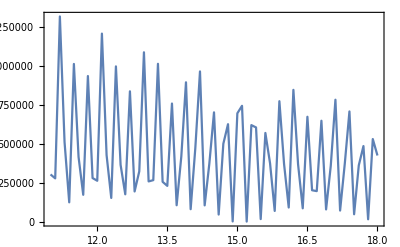
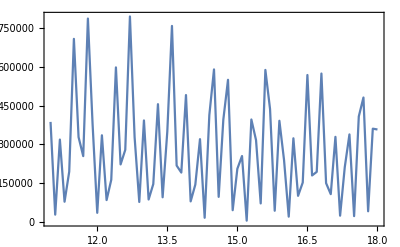

```mathematica
{ListLinePlot[tk02,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[tk02m,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
ParallelTable[dProbabPlane[1,x/mee,1/γ,1/γ],{x,1,2,0.05}]//AbsoluteTiming
```

{16.6569,{6.32595×10^6,8.04833×10^6,7.60734×10^6,5.34935×10^6,2.45492×10^6,385906.,156093.,1.72039×10^6,4.04096×10^6,5.75948×10^6,5.92241×10^6,4.44712×10^6,2.18014×10^6,407201.,79109.,1.29921×10^6,3.31154×10^6,4.9242×10^6,5.19799×10^6,4.00629×10^6,2.06202×10^6}}

```mathematica
(*старое*)
```

```mathematica
dProbabPlane[1,1.5/mee,1/γ,1/γ]//Timing
dProbabPlane[1,1.6/mee,1/γ,1/γ]//Timing
dProbabPlane[1,1.4/mee,1/γ,1/γ]//Timing
```

{1.49761,5.92241×10^6}

{1.54441,2.18014×10^6}

{1.41961,4.04096×10^6}

```mathematica
ParallelTable[dProbabPlane[1,x/mee,1/γ,1/γ],{x,1,2,0.1}]//AbsoluteTiming
```

{8.80227,{6.32595×10^6,7.60734×10^6,2.45492×10^6,156093.,4.04096×10^6,5.92241×10^6,2.18014×10^6,79109.,3.31154×10^6,5.19799×10^6,2.06202×10^6}}

```mathematica
(*---старое----*)
```

```mathematica
dProbabPlane[1,1.5/mee,1/γ,1/γ]//Timing
dProbabPlane[1,1.6/mee,1/γ,1/γ]//Timing
dProbabPlane[1,1.4/mee,1/γ,1/γ]//Timing
```

{1.45081,5.92241×10^6}

{1.56001,2.18014×10^6}

{1.43521,4.04096×10^6}

```mathematica
ParallelTable[dProbabPlane[1,x/mee,1/γ,1/γ],{x,1,2,0.1}]//AbsoluteTiming
```

{8.34059,{6.32595×10^6,7.60734×10^6,2.45492×10^6,156093.,4.04096×10^6,5.92241×10^6,2.18014×10^6,79109.,3.31154×10^6,5.19799×10^6,2.06202×10^6}}

```mathematica
(*------------мусор------------*)
```

```mathematica
ff[x_]=Sin[x];
```

```mathematica
ff[1]//N
ff[2]//N
```

0.841471

0.909297

```mathematica
ee={1,0}
```

{1,0}

```mathematica
ff1[x_]:=Evaluate[x.ee]
```

```mathematica
ff1[{2,1}]//RepeatedTiming
```

{2.27×10^-6,2}

```mathematica
ff2[x_]=x.ee;
```

```mathematica
ff2[{2,1}]//RepeatedTiming
```

{2.18×10^-6,2}

```mathematica
ff3[x_]:=x.ee
```

```mathematica
ff3[{2,1}]//RepeatedTiming
```

{2.7×10^-6,2}

```mathematica
Clear[ff4]
```

```mathematica
ff4[x_?NumberQ]=Sin[x]
```

sin(x)

```mathematica
ff4[a]
```

ff4(a)

```mathematica
ff4[1]
```

sin(1)

```mathematica
ff4[1]
```

sin(x$1168)

```mathematica
ff41[x_]=Sin[x]
```

sin(x)

```mathematica
ff4[2]//RepeatedTiming
ff41[2]//RepeatedTiming
```

{1.×10^-6,sin(2)}

{8.5×10^-7,sin(2)}

```mathematica
ff5[x_]=ff41[x];
```

```mathematica
ff5[1]
```

sin(1)